# SVM-BDS-BDT Comparison Results, 9/14/16

## Raw Data

## SVM: c, γ, False Positive Fraction, False Negative Fraction, Efficiency, Distance, Time

```mathematica
SVMLinearHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","LinearHardTestingAll0914"}],"Table"];
SVMLinearHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","LinearHardTestingSignal0914"}],"Table"];
SVMLinearHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","LinearHardTestingBackground0914"}],"Table"];

SVMLinearSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","LinearSoftTestingAll0914"}],"Table"];
SVMLinearSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","LinearSoftTestingSignal0914"}],"Table"];
SVMLinearSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","LinearSoftTestingBackground0914"}],"Table"];


SVMCircleHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","CircleHardTestingAll0914"}],"Table"];
SVMCircleHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","CircleHardTestingSignal0914"}],"Table"];
SVMCircleHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","CircleHardTestingBackground0914"}],"Table"];

SVMCircleSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","CircleSoftTestingAll0914"}],"Table"];
SVMCircleSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","CircleSoftTestingSignal0914"}],"Table"];
SVMCircleSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","CircleSoftTestingBackground0914"}],"Table"];


SVMTwoCircleHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","TwoCircleHardTestingAll0914"}],"Table"];
SVMTwoCircleHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","TwoCircleHardTestingSignal0914"}],"Table"];
SVMTwoCircleHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","TwoCircleHardTestingBackground0914"}],"Table"];

SVMTwoCircleSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","TwoCircleSoftTestingAll0914"}],"Table"];
SVMTwoCircleSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","TwoCircleSoftTestingSignal0914"}],"Table"];
SVMTwoCircleSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","TwoCircleSoftTestingBackground0914"}],"Table"];


SVMPlaneHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","PlaneHardTestingAll0914"}],"Table"];
SVMPlaneHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","PlaneHardTestingSignal0914"}],"Table"];
SVMPlaneHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","PlaneHardTestingBackground0914"}],"Table"];

SVMPlaneSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","PlaneSoftTestingAll0914"}],"Table"];
SVMPlaneSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","PlaneSoftTestingSignal0914"}],"Table"];
SVMPlaneSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","PlaneSoftTestingBackground0914"}],"Table"];


SVMSphereHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","SphereHardTestingAll0914"}],"Table"];
SVMSphereHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","SphereHardTestingSignal0914"}],"Table"];
SVMSphereHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","SphereHardTestingBackground0914"}],"Table"];

SVMSphereSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","SphereSoftTestingAll0914"}],"Table"];
SVMSphereSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","SphereSoftTestingSignal0914"}],"Table"];
SVMSphereSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","SphereSoftTestingBackground0914"}],"Table"];


SVMTwoSphereHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","TwoSphereHardTestingAll0914"}],"Table"];
SVMTwoSphereHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","TwoSphereHardTestingSignal0914"}],"Table"];
SVMTwoSphereHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","TwoSphereHardTestingBackground0914"}],"Table"];

SVMTwoSphereSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","TwoSphereSoftTestingAll0914"}],"Table"];
SVMTwoSphereSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","TwoSphereSoftTestingSignal0914"}],"Table"];
SVMTwoSphereSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","TwoSphereSoftTestingBackground0914"}],"Table"];


SVM8DHyperplaneHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","8DHyperplaneHardTestingAll0914"}],"Table"];
SVM8DHyperplaneHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","8DHyperplaneHardTestingSignal0914"}],"Table"];
SVM8DHyperplaneHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","8DHyperplaneHardTestingBackground0914"}],"Table"];

SVM8DHyperplaneSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","8DHyperplaneSoftTestingAll0914"}],"Table"];
SVM8DHyperplaneSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","8DHyperplaneSoftTestingSignal0914"}],"Table"];
SVM8DHyperplaneSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","8DHyperplaneSoftTestingBackground0914"}],"Table"];


SVM8DHypersphereHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","8DHypersphereHardTestingAll0914"}],"Table"];
SVM8DHypersphereHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","8DHypersphereHardTestingSignal0914"}],"Table"];
SVM8DHypersphereHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","8DHypersphereHardTestingBackground0914"}],"Table"];

SVM8DHypersphereSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","8DHypersphereSoftTestingAll0914"}],"Table"];
SVM8DHypersphereSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","8DHypersphereSoftTestingSignal0914"}],"Table"];
SVM8DHypersphereSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","8DHypersphereSoftTestingBackground0914"}],"Table"];


SVM8DTwoHypersphereHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","8DTwoHypersphereHardTestingAll0914"}],"Table"];
SVM8DTwoHypersphereHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","8DTwoHypersphereHardTestingSignal0914"}],"Table"];
SVM8DTwoHypersphereHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","8DTwoHypersphereHardTestingBackground0914"}],"Table"];

SVM8DTwoHypersphereSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","8DTwoHypersphereSoftTestingAll0914"}],"Table"];
SVM8DTwoHypersphereSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","8DTwoHypersphereSoftTestingSignal0914"}],"Table"];
SVM8DTwoHypersphereSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","8DTwoHypersphereSoftTestingBackground0914"}],"Table"];


SVMMonteCarloTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","MonteCarloTestingAll0914"}],"Table"];
SVMMonteCarloTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","MonteCarloTestingSignal0914"}],"Table"];
SVMMonteCarloTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","MonteCarloTestingBackground0914"}],"Table"];

SVMAllRawData={SVMLinearHardTestingAllRawData,SVMLinearHardTestingSignalRawData,SVMLinearHardTestingBackgroundRawData,SVMLinearSoftTestingAllRawData,SVMLinearSoftTestingSignalRawData,SVMLinearSoftTestingBackgroundRawData,SVMCircleHardTestingAllRawData,SVMCircleHardTestingSignalRawData,SVMCircleHardTestingBackgroundRawData,SVMCircleSoftTestingAllRawData,SVMCircleSoftTestingSignalRawData,SVMCircleSoftTestingBackgroundRawData,SVMTwoCircleHardTestingAllRawData,SVMTwoCircleHardTestingSignalRawData,SVMTwoCircleHardTestingBackgroundRawData,SVMTwoCircleSoftTestingAllRawData,SVMTwoCircleSoftTestingSignalRawData,SVMTwoCircleSoftTestingBackgroundRawData,SVMPlaneHardTestingAllRawData,SVMPlaneHardTestingSignalRawData,SVMPlaneHardTestingBackgroundRawData,SVMPlaneSoftTestingAllRawData,SVMPlaneSoftTestingSignalRawData,SVMPlaneSoftTestingBackgroundRawData,SVMSphereHardTestingAllRawData,SVMSphereHardTestingSignalRawData,SVMSphereHardTestingBackgroundRawData,SVMSphereSoftTestingAllRawData,SVMSphereSoftTestingSignalRawData,SVMSphereSoftTestingBackgroundRawData,SVMTwoSphereHardTestingAllRawData,SVMTwoSphereHardTestingSignalRawData,SVMTwoSphereHardTestingBackgroundRawData,SVMTwoSphereSoftTestingAllRawData,SVMTwoSphereSoftTestingSignalRawData,SVMTwoSphereSoftTestingBackgroundRawData,SVM8DHyperplaneHardTestingAllRawData,SVM8DHyperplaneHardTestingSignalRawData,SVM8DHyperplaneHardTestingBackgroundRawData,SVM8DHyperplaneSoftTestingAllRawData,SVM8DHyperplaneSoftTestingSignalRawData,SVM8DHyperplaneSoftTestingBackgroundRawData,SVM8DHypersphereHardTestingAllRawData,SVM8DHypersphereHardTestingSignalRawData,SVM8DHypersphereHardTestingBackgroundRawData,SVM8DHypersphereSoftTestingAllRawData,SVM8DHypersphereSoftTestingSignalRawData,SVM8DHypersphereSoftTestingBackgroundRawData,SVM8DTwoHypersphereHardTestingAllRawData,SVM8DTwoHypersphereHardTestingSignalRawData,SVM8DTwoHypersphereHardTestingBackgroundRawData,SVM8DTwoHypersphereSoftTestingAllRawData,SVM8DTwoHypersphereSoftTestingSignalRawData,SVM8DTwoHypersphereSoftTestingBackgroundRawData,SVMMonteCarloTestingAllRawData,SVMMonteCarloTestingSignalRawData,SVMMonteCarloTestingBackgroundRawData};

SVMAllDataTypes={"Linear Hard Testing All","Linear Hard Testing Signal","Linear Hard Testing Background","Linear Soft Testing All","Linear Soft Testing Signal","Linear Soft Testing Background","Circle Hard Testing All","Circle Hard Testing Signal","Circle Hard Testing Background","Circle Soft Testing All","Circle Soft Testing Signal","Circle Soft Testing Background","Two Circle Hard Testing All","Two Circle Hard Testing Signal","Two Circle Hard Testing Background","Two Circle Soft Testing All","Two Circle Soft Testing Signal","Two Circle Soft Testing Background","Plane Hard Testing All","Plane Hard Testing Signal","Plane Hard Testing Background","Plane Soft Testing All","Plane Soft Testing Signal","Plane Soft Testing Background","Sphere Hard Testing All","Sphere Hard Testing Signal","Sphere Hard Testing Background","Sphere Soft Testing All","Sphere Soft Testing Signal","Sphere Soft Testing Background","Two Sphere Hard Testing All","Two Sphere Hard Testing Signal","Two Sphere Hard Testing Background","Two Sphere Soft Testing All","Two Sphere Soft Testing Signal","Two Sphere Soft Testing Background","8D Hyperplane Hard Testing All","8D Hyperplane Hard Testing Signal","8D Hyperplane Hard Testing Background","8D Hyperplane Soft Testing All","8D Hyperplane Soft Testing Signal","8D Hyperplane Soft Testing Background","8D Hypersphere Hard Testing All","8D Hypersphere Hard Testing Signal","8D Hypersphere Hard Testing Background","8D Hypersphere Soft Testing All","8D Hypersphere Soft Testing Signal","8D Hypersphere Soft Testing Background","8D Two Hypersphere Hard Testing All","8D Two Hypersphere Hard Testing Signal","8D Two Hypersphere Hard Testing Background","8D Two Hypersphere Soft Testing All","8D Two Hypersphere Soft Testing Signal","8D Two Hypersphere Soft Testing Background", "Monte Carlo Testing All", "Monte Carlo Testing Signal", "Monte Carlo Testing Background"};
```

## BDS: Number of Stumps, Efficiency, False Positive Fraction, False Negative Fraction, Distance, Time

```mathematica
BDSLinearHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","LinearHardTestingAll0914"}],"Table"];
BDSLinearHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","LinearHardTestingSignal0914"}],"Table"];
BDSLinearHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","LinearHardTestingBackground0914"}],"Table"];

BDSLinearSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","LinearSoftTestingAll0914"}],"Table"];
BDSLinearSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","LinearSoftTestingSignal0914"}],"Table"];
BDSLinearSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","LinearSoftTestingBackground0914"}],"Table"];


BDSCircleHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","CircleHardTestingAll0914"}],"Table"];
BDSCircleHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","CircleHardTestingSignal0914"}],"Table"];
BDSCircleHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","CircleHardTestingBackground0914"}],"Table"];

BDSCircleSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","CircleSoftTestingAll0914"}],"Table"];
BDSCircleSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","CircleSoftTestingSignal0914"}],"Table"];
BDSCircleSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","CircleSoftTestingBackground0914"}],"Table"];


BDSTwoCircleHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","TwoCircleHardTestingAll0914"}],"Table"];
BDSTwoCircleHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","TwoCircleHardTestingSignal0914"}],"Table"];
BDSTwoCircleHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","TwoCircleHardTestingBackground0914"}],"Table"];

BDSTwoCircleSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","TwoCircleSoftTestingAll0914"}],"Table"];
BDSTwoCircleSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","TwoCircleSoftTestingSignal0914"}],"Table"];
BDSTwoCircleSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","TwoCircleSoftTestingBackground0914"}],"Table"];


BDSPlaneHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","PlaneHardTestingAll0914"}],"Table"];
BDSPlaneHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","PlaneHardTestingSignal0914"}],"Table"];
BDSPlaneHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","PlaneHardTestingBackground0914"}],"Table"];

BDSPlaneSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","PlaneSoftTestingAll0914"}],"Table"];
BDSPlaneSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","PlaneSoftTestingSignal0914"}],"Table"];
BDSPlaneSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","PlaneSoftTestingBackground0914"}],"Table"];


BDSSphereHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","SphereHardTestingAll0914"}],"Table"];
BDSSphereHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","SphereHardTestingSignal0914"}],"Table"];
BDSSphereHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","SphereHardTestingBackground0914"}],"Table"];

BDSSphereSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","SphereSoftTestingAll0914"}],"Table"];
BDSSphereSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","SphereSoftTestingSignal0914"}],"Table"];
BDSSphereSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","SphereSoftTestingBackground0914"}],"Table"];


BDSTwoSphereHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","TwoSphereHardTestingAll0914"}],"Table"];
BDSTwoSphereHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","TwoSphereHardTestingSignal0914"}],"Table"];
BDSTwoSphereHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","TwoSphereHardTestingBackground0914"}],"Table"];

BDSTwoSphereSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","TwoSphereSoftTestingAll0914"}],"Table"];
BDSTwoSphereSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","TwoSphereSoftTestingSignal0914"}],"Table"];
BDSTwoSphereSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","TwoSphereSoftTestingBackground0914"}],"Table"];


BDS8DHyperplaneHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","8DHyperplaneHardTestingAll0914"}],"Table"];
BDS8DHyperplaneHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","8DHyperplaneHardTestingSignal0914"}],"Table"];
BDS8DHyperplaneHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","8DHyperplaneHardTestingBackground0914"}],"Table"];

BDS8DHyperplaneSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","8DHyperplaneSoftTestingAll0914"}],"Table"];
BDS8DHyperplaneSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","8DHyperplaneSoftTestingSignal0914"}],"Table"];
BDS8DHyperplaneSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","8DHyperplaneSoftTestingBackground0914"}],"Table"];


BDS8DHypersphereHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","8DHypersphereHardTestingAll0914"}],"Table"];
BDS8DHypersphereHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","8DHypersphereHardTestingSignal0914"}],"Table"];
BDS8DHypersphereHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","8DHypersphereHardTestingBackground0914"}],"Table"];

BDS8DHypersphereSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","8DHypersphereSoftTestingAll0914"}],"Table"];
BDS8DHypersphereSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","8DHypersphereSoftTestingSignal0914"}],"Table"];
BDS8DHypersphereSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","8DHypersphereSoftTestingBackground0914"}],"Table"];


BDS8DTwoHypersphereHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","8DTwoHypersphereHardTestingAll0914"}],"Table"];
BDS8DTwoHypersphereHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","8DTwoHypersphereHardTestingSignal0914"}],"Table"];
BDS8DTwoHypersphereHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","8DTwoHypersphereHardTestingBackground0914"}],"Table"];

BDS8DTwoHypersphereSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","8DTwoHypersphereSoftTestingAll0914"}],"Table"];
BDS8DTwoHypersphereSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","8DTwoHypersphereSoftTestingSignal0914"}],"Table"];
BDS8DTwoHypersphereSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","8DTwoHypersphereSoftTestingBackground0914"}],"Table"];


BDSMonteCarloTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","MonteCarloTestingAll0914"}],"Table"];
BDSMonteCarloTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","MonteCarloTestingSignal0914"}],"Table"];
BDSMonteCarloTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","MonteCarloTestingBackground0914"}],"Table"];


BDSAllRawData={BDSLinearHardTestingAllRawData,BDSLinearHardTestingSignalRawData,BDSLinearHardTestingBackgroundRawData,BDSLinearSoftTestingAllRawData,BDSLinearSoftTestingSignalRawData,BDSLinearSoftTestingBackgroundRawData,BDSCircleHardTestingAllRawData,BDSCircleHardTestingSignalRawData,BDSCircleHardTestingBackgroundRawData,BDSCircleSoftTestingAllRawData,BDSCircleSoftTestingSignalRawData,BDSCircleSoftTestingBackgroundRawData,BDSTwoCircleHardTestingAllRawData,BDSTwoCircleHardTestingSignalRawData,BDSTwoCircleHardTestingBackgroundRawData,BDSTwoCircleSoftTestingAllRawData,BDSTwoCircleSoftTestingSignalRawData,BDSTwoCircleSoftTestingBackgroundRawData,BDSPlaneHardTestingAllRawData,BDSPlaneHardTestingSignalRawData,BDSPlaneHardTestingBackgroundRawData,BDSPlaneSoftTestingAllRawData,BDSPlaneSoftTestingSignalRawData,BDSPlaneSoftTestingBackgroundRawData,BDSSphereHardTestingAllRawData,BDSSphereHardTestingSignalRawData,BDSSphereHardTestingBackgroundRawData,BDSSphereSoftTestingAllRawData,BDSSphereSoftTestingSignalRawData,BDSSphereSoftTestingBackgroundRawData,BDSTwoSphereHardTestingAllRawData,BDSTwoSphereHardTestingSignalRawData,BDSTwoSphereHardTestingBackgroundRawData,BDSTwoSphereSoftTestingAllRawData,BDSTwoSphereSoftTestingSignalRawData,BDSTwoSphereSoftTestingBackgroundRawData,BDS8DHyperplaneHardTestingAllRawData,BDS8DHyperplaneHardTestingSignalRawData,BDS8DHyperplaneHardTestingBackgroundRawData,BDS8DHyperplaneSoftTestingAllRawData,BDS8DHyperplaneSoftTestingSignalRawData,BDS8DHyperplaneSoftTestingBackgroundRawData,BDS8DHypersphereHardTestingAllRawData,BDS8DHypersphereHardTestingSignalRawData,BDS8DHypersphereHardTestingBackgroundRawData,BDS8DHypersphereSoftTestingAllRawData,BDS8DHypersphereSoftTestingSignalRawData,BDS8DHypersphereSoftTestingBackgroundRawData,BDS8DTwoHypersphereHardTestingAllRawData,BDS8DTwoHypersphereHardTestingSignalRawData,BDS8DTwoHypersphereHardTestingBackgroundRawData,BDS8DTwoHypersphereSoftTestingAllRawData,BDS8DTwoHypersphereSoftTestingSignalRawData,BDS8DTwoHypersphereSoftTestingBackgroundRawData,BDSMonteCarloTestingAllRawData,BDSMonteCarloTestingSignalRawData,BDSMonteCarloTestingBackgroundRawData};

BDSAllDataTypes={"Linear Hard Testing All","Linear Hard Testing Signal","Linear Hard Testing Background","Linear Soft Testing All","Linear Soft Testing Signal","Linear Soft Testing Background","Circle Hard Testing All","Circle Hard Testing Signal","Circle Hard Testing Background","Circle Soft Testing All","Circle Soft Testing Signal","Circle Soft Testing Background","Two Circle Hard Testing All","Two Circle Hard Testing Signal","Two Circle Hard Testing Background","Two Circle Soft Testing All","Two Circle Soft Testing Signal","Two Circle Soft Testing Background","Plane Hard Testing All","Plane Hard Testing Signal","Plane Hard Testing Background","Plane Soft Testing All","Plane Soft Testing Signal","Plane Soft Testing Background","Sphere Hard Testing All","Sphere Hard Testing Signal","Sphere Hard Testing Background","Sphere Soft Testing All","Sphere Soft Testing Signal","Sphere Soft Testing Background","Two Sphere Hard Testing All","Two Sphere Hard Testing Signal","Two Sphere Hard Testing Background","Two Sphere Soft Testing All","Two Sphere Soft Testing Signal","Two Sphere Soft Testing Background","8D Hyperplane Hard Testing All","8D Hyperplane Hard Testing Signal","8D Hyperplane Hard Testing Background","8D Hyperplane Soft Testing All","8D Hyperplane Soft Testing Signal","8D Hyperplane Soft Testing Background","8D Hypersphere Hard Testing All","8D Hypersphere Hard Testing Signal","8D Hypersphere Hard Testing Background","8D Hypersphere Soft Testing All","8D Hypersphere Soft Testing Signal","8D Hypersphere Soft Testing Background","8D Two Hypersphere Hard Testing All","8D Two Hypersphere Hard Testing Signal","8D Two Hypersphere Hard Testing Background","8D Two Hypersphere Soft Testing All","8D Two Hypersphere Soft Testing Signal","8D Two Hypersphere Soft Testing Background","Monte Carlo Testing All","Monte Carlo Testing All","Monte Carlo Testing All"};
```

## BDT: Number of Trees, Efficiency, False Positive Fraction, False Negative Fraction, Distance, Time

```mathematica
BDTLinearHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","LinearHardTestingAll0914"}],"Table"];
BDTLinearHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","LinearHardTestingSignal0914"}],"Table"];
BDTLinearHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","LinearHardTestingBackground0914"}],"Table"];

BDTLinearSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","LinearSoftTestingAll0914"}],"Table"];
BDTLinearSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","LinearSoftTestingSignal0914"}],"Table"];
BDTLinearSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","LinearSoftTestingBackground0914"}],"Table"];


BDTCircleHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","CircleHardTestingAll0914"}],"Table"];
BDTCircleHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","CircleHardTestingSignal0914"}],"Table"];
BDTCircleHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","CircleHardTestingBackground0914"}],"Table"];

BDTCircleSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","CircleSoftTestingAll0914"}],"Table"];
BDTCircleSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","CircleSoftTestingSignal0914"}],"Table"];
BDTCircleSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","CircleSoftTestingBackground0914"}],"Table"];


BDTTwoCircleHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","TwoCircleHardTestingAll0914"}],"Table"];
BDTTwoCircleHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","TwoCircleHardTestingSignal0914"}],"Table"];
BDTTwoCircleHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","TwoCircleHardTestingBackground0914"}],"Table"];

BDTTwoCircleSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","TwoCircleSoftTestingAll0914"}],"Table"];
BDTTwoCircleSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","TwoCircleSoftTestingSignal0914"}],"Table"];
BDTTwoCircleSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","TwoCircleSoftTestingBackground0914"}],"Table"];


BDTPlaneHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","PlaneHardTestingAll0914"}],"Table"];
BDTPlaneHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","PlaneHardTestingSignal0914"}],"Table"];
BDTPlaneHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","PlaneHardTestingBackground0914"}],"Table"];

BDTPlaneSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","PlaneSoftTestingAll0914"}],"Table"];
BDTPlaneSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","PlaneSoftTestingSignal0914"}],"Table"];
BDTPlaneSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","PlaneSoftTestingBackground0914"}],"Table"];


BDTSphereHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","SphereHardTestingAll0914"}],"Table"];
BDTSphereHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","SphereHardTestingSignal0914"}],"Table"];
BDTSphereHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","SphereHardTestingBackground0914"}],"Table"];

BDTSphereSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","SphereSoftTestingAll0914"}],"Table"];
BDTSphereSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","SphereSoftTestingSignal0914"}],"Table"];
BDTSphereSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","SphereSoftTestingBackground0914"}],"Table"];


BDTTwoSphereHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","TwoSphereHardTestingAll0914"}],"Table"];
BDTTwoSphereHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","TwoSphereHardTestingSignal0914"}],"Table"];
BDTTwoSphereHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","TwoSphereHardTestingBackground0914"}],"Table"];

BDTTwoSphereSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","TwoSphereSoftTestingAll0914"}],"Table"];
BDTTwoSphereSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","TwoSphereSoftTestingSignal0914"}],"Table"];
BDTTwoSphereSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","TwoSphereSoftTestingBackground0914"}],"Table"];


BDT8DHyperplaneHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","8DHyperplaneHardTestingAll0914"}],"Table"];
BDT8DHyperplaneHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","8DHyperplaneHardTestingSignal0914"}],"Table"];
BDT8DHyperplaneHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","8DHyperplaneHardTestingBackground0914"}],"Table"];

BDT8DHyperplaneSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","8DHyperplaneSoftTestingAll0914"}],"Table"];
BDT8DHyperplaneSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","8DHyperplaneSoftTestingSignal0914"}],"Table"];
BDT8DHyperplaneSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","8DHyperplaneSoftTestingBackground0914"}],"Table"];


BDT8DHypersphereHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","8DHypersphereHardTestingAll0914"}],"Table"];
BDT8DHypersphereHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","8DHypersphereHardTestingSignal0914"}],"Table"];
BDT8DHypersphereHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","8DHypersphereHardTestingBackground0914"}],"Table"];

BDT8DHypersphereSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","8DHypersphereSoftTestingAll0914"}],"Table"];
BDT8DHypersphereSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","8DHypersphereSoftTestingSignal0914"}],"Table"];
BDT8DHypersphereSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","8DHypersphereSoftTestingBackground0914"}],"Table"];


BDT8DTwoHypersphereHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","8DTwoHypersphereHardTestingAll0914"}],"Table"];
BDT8DTwoHypersphereHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","8DTwoHypersphereHardTestingSignal0914"}],"Table"];
BDT8DTwoHypersphereHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","8DTwoHypersphereHardTestingBackground0914"}],"Table"];

BDT8DTwoHypersphereSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","8DTwoHypersphereSoftTestingAll0914"}],"Table"];
BDT8DTwoHypersphereSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","8DTwoHypersphereSoftTestingSignal0914"}],"Table"];
BDT8DTwoHypersphereSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","8DTwoHypersphereSoftTestingBackground0914"}],"Table"];

BDTMonteCarloTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","MonteCarloTestingAll0914"}],"Table"];
BDTMonteCarloTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","MonteCarloTestingSignal0914"}],"Table"];
BDTMonteCarloTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","MonteCarloTestingBackground0914"}],"Table"];

BDTAllRawData={BDTLinearHardTestingAllRawData,BDTLinearHardTestingSignalRawData,BDTLinearHardTestingBackgroundRawData,BDTLinearSoftTestingAllRawData,BDTLinearSoftTestingSignalRawData,BDTLinearSoftTestingBackgroundRawData,BDTCircleHardTestingAllRawData,BDTCircleHardTestingSignalRawData,BDTCircleHardTestingBackgroundRawData,BDTCircleSoftTestingAllRawData,BDTCircleSoftTestingSignalRawData,BDTCircleSoftTestingBackgroundRawData,BDTTwoCircleHardTestingAllRawData,BDTTwoCircleHardTestingSignalRawData,BDTTwoCircleHardTestingBackgroundRawData,BDTTwoCircleSoftTestingAllRawData,BDTTwoCircleSoftTestingSignalRawData,BDTTwoCircleSoftTestingBackgroundRawData,BDTPlaneHardTestingAllRawData,BDTPlaneHardTestingSignalRawData,BDTPlaneHardTestingBackgroundRawData,BDTPlaneSoftTestingAllRawData,BDTPlaneSoftTestingSignalRawData,BDTPlaneSoftTestingBackgroundRawData,BDTSphereHardTestingAllRawData,BDTSphereHardTestingSignalRawData,BDTSphereHardTestingBackgroundRawData,BDTSphereSoftTestingAllRawData,BDTSphereSoftTestingSignalRawData,BDTSphereSoftTestingBackgroundRawData,BDTTwoSphereHardTestingAllRawData,BDTTwoSphereHardTestingSignalRawData,BDTTwoSphereHardTestingBackgroundRawData,BDTTwoSphereSoftTestingAllRawData,BDTTwoSphereSoftTestingSignalRawData,BDTTwoSphereSoftTestingBackgroundRawData,BDT8DHyperplaneHardTestingAllRawData,BDT8DHyperplaneHardTestingSignalRawData,BDT8DHyperplaneHardTestingBackgroundRawData,BDT8DHyperplaneSoftTestingAllRawData,BDT8DHyperplaneSoftTestingSignalRawData,BDT8DHyperplaneSoftTestingBackgroundRawData,BDT8DHypersphereHardTestingAllRawData,BDT8DHypersphereHardTestingSignalRawData,BDT8DHypersphereHardTestingBackgroundRawData,BDT8DHypersphereSoftTestingAllRawData,BDT8DHypersphereSoftTestingSignalRawData,BDT8DHypersphereSoftTestingBackgroundRawData,BDT8DTwoHypersphereHardTestingAllRawData,BDT8DTwoHypersphereHardTestingSignalRawData,BDT8DTwoHypersphereHardTestingBackgroundRawData,BDT8DTwoHypersphereSoftTestingAllRawData,BDT8DTwoHypersphereSoftTestingSignalRawData,BDT8DTwoHypersphereSoftTestingBackgroundRawData, BDTMonteCarloTestingAllRawData,BDTMonteCarloTestingSignalRawData,BDTMonteCarloTestingBackgroundRawData};

BDTAllDataTypes={"Linear Hard Testing All","Linear Hard Testing Signal","Linear Hard Testing Background","Linear Soft Testing All","Linear Soft Testing Signal","Linear Soft Testing Background","Circle Hard Testing All","Circle Hard Testing Signal","Circle Hard Testing Background","Circle Soft Testing All","Circle Soft Testing Signal","Circle Soft Testing Background","Two Circle Hard Testing All","Two Circle Hard Testing Signal","Two Circle Hard Testing Background","Two Circle Soft Testing All","Two Circle Soft Testing Signal","Two Circle Soft Testing Background","Plane Hard Testing All","Plane Hard Testing Signal","Plane Hard Testing Background","Plane Soft Testing All","Plane Soft Testing Signal","Plane Soft Testing Background","Sphere Hard Testing All","Sphere Hard Testing Signal","Sphere Hard Testing Background","Sphere Soft Testing All","Sphere Soft Testing Signal","Sphere Soft Testing Background","Two Sphere Hard Testing All","Two Sphere Hard Testing Signal","Two Sphere Hard Testing Background","Two Sphere Soft Testing All","Two Sphere Soft Testing Signal","Two Sphere Soft Testing Background","8D Hyperplane Hard Testing All","8D Hyperplane Hard Testing Signal","8D Hyperplane Hard Testing Background","8D Hyperplane Soft Testing All","8D Hyperplane Soft Testing Signal","8D Hyperplane Soft Testing Background","8D Hypersphere Hard Testing All","8D Hypersphere Hard Testing Signal","8D Hypersphere Hard Testing Background","8D Hypersphere Soft Testing All","8D Hypersphere Soft Testing Signal","8D Hypersphere Soft Testing Background","8D Two Hypersphere Hard Testing All","8D Two Hypersphere Hard Testing Signal","8D Two Hypersphere Hard Testing Background","8D Two Hypersphere Soft Testing All","8D Two Hypersphere Soft Testing Signal","8D Two Hypersphere Soft Testing Background","Monte Carlo Testing All","Monte Carlo Testing All","Monte Carlo Testing All"};
```

## Formatted Datasets

## SVM

### c-γ-Efficiency

```mathematica
SVMCGE[RawData_]:=RawData[[All,{1,2, 6}]]
```

### Log(c)-γ-Efficiency

```mathematica
SVMLogCGE[RawData_]:=MapAt[Log10, RawData[[All,{1,2, 6}]], {All, 1}]
```

### c-γ-Distance

```mathematica
SVMCGD[RawData_]:=RawData[[All,{1,2, 7}]]
```

### Log(c)-γ-Distance

```mathematica
SVMLogCGD[RawData_]:=MapAt[Log10, RawData[[All,{1,2, 7}]], {All, 1}]
```

### False Positive Fraction-Efficiency

```mathematica
SVMFPE[RawData_]:= RawData[[All,{4,6}]]
```

## BDS

### Number of Stumps-Efficiency

```mathematica
BDSSE[RawData_]:=RawData[[All,{1,2}]]
```

### Number of Stumps-Distance

```mathematica
BDSSD[RawData_]:=RawData[[All,{1,5}]]
```

### False Positive Fraction-Efficiency

```mathematica
BDSFPE[RawData_]:= RawData[[All,{3,2}]]
```

## BDT

### Number of Trees-Efficiency

```mathematica
BDTTE[RawData_]:=RawData[[All,{1,2}]]
```

### Number of Trees-Distance

```mathematica
BDTTD[RawData_]:=RawData[[All,{1,5}]]
```

### False Positive Fraction-Efficiency

```mathematica
BDTFPE[RawData_]:= RawData[[All,{3,2}]]
```

## Optimizing Parameters

## SVM

### Overall

```mathematica
SVMBest[RawData_]:=First[SortBy[RawData[[All,{7,1,2,5,4,6}]],Last]];
```

```mathematica
SVMBestResultTable=Grid[{{"Data Set","Runtime (s)","c","γ","Efficiency","False Negative Fraction","Distance"},Prepend[SVMBest[SVMLinearHardTestingAllRawData],"Linear Hard Testing All"],Prepend[SVMBest[SVMLinearHardTestingSignalRawData],"Linear Hard Testing Signal"],Prepend[SVMBest[SVMLinearHardTestingBackgroundRawData],"Linear Hard Testing Background"],Prepend[SVMBest[SVMLinearSoftTestingAllRawData],"Linear Soft Testing All"],Prepend[SVMBest[SVMLinearSoftTestingSignalRawData],"Linear Soft Testing Signal"],Prepend[SVMBest[SVMLinearSoftTestingBackgroundRawData],"Linear Soft Testing Background"],Prepend[SVMBest[SVMCircleHardTestingAllRawData],"Circle Hard Testing All"],Prepend[SVMBest[SVMCircleHardTestingSignalRawData],"Circle Hard Testing Signal"],Prepend[SVMBest[SVMCircleHardTestingBackgroundRawData],"Circle Hard Testing Background"],Prepend[SVMBest[SVMCircleSoftTestingAllRawData],"Circle Soft Testing All"],Prepend[SVMBest[SVMCircleSoftTestingSignalRawData],"Circle Soft Testing Signal"],Prepend[SVMBest[SVMCircleSoftTestingBackgroundRawData],"Circle Soft Testing Background"],Prepend[SVMBest[SVMTwoCircleHardTestingAllRawData],"Two Circle Hard Testing All"],Prepend[SVMBest[SVMTwoCircleHardTestingSignalRawData],"Two Circle Hard Testing Signal"],Prepend[SVMBest[SVMTwoCircleHardTestingBackgroundRawData],"Two Circle Hard Testing Background"],Prepend[SVMBest[SVMTwoCircleSoftTestingAllRawData],"Two Circle Soft Testing All"],Prepend[SVMBest[SVMTwoCircleSoftTestingSignalRawData],"Two Circle Soft Testing Signal"],Prepend[SVMBest[SVMTwoCircleSoftTestingBackgroundRawData],"Two Circle Soft Testing Background"],Prepend[SVMBest[SVMPlaneHardTestingAllRawData],"Plane Hard Testing All"],Prepend[SVMBest[SVMPlaneHardTestingSignalRawData],"Plane Hard Testing Signal"],Prepend[SVMBest[SVMPlaneHardTestingBackgroundRawData],"Plane Hard Testing Background"],Prepend[SVMBest[SVMPlaneSoftTestingAllRawData],"Plane Soft Testing All"],Prepend[SVMBest[SVMPlaneSoftTestingSignalRawData],"Plane Soft Testing Signal"],Prepend[SVMBest[SVMPlaneSoftTestingBackgroundRawData],"Plane Soft Testing Background"],Prepend[SVMBest[SVMSphereHardTestingAllRawData],"Sphere Hard Testing All"],Prepend[SVMBest[SVMSphereHardTestingSignalRawData],"Sphere Hard Testing Signal"],Prepend[SVMBest[SVMSphereHardTestingBackgroundRawData],"Sphere Hard Testing Background"],Prepend[SVMBest[SVMSphereSoftTestingAllRawData],"Sphere Soft Testing All"],Prepend[SVMBest[SVMSphereSoftTestingSignalRawData],"Sphere Soft Testing Signal"],Prepend[SVMBest[SVMSphereSoftTestingBackgroundRawData],"Sphere Soft Testing Background"],Prepend[SVMBest[SVMTwoSphereHardTestingAllRawData],"Two Sphere Hard Testing All"],Prepend[SVMBest[SVMTwoSphereHardTestingSignalRawData],"Two Sphere Hard Testing Signal"],Prepend[SVMBest[SVMTwoSphereHardTestingBackgroundRawData],"Two Sphere Hard Testing Background"],Prepend[SVMBest[SVMTwoSphereSoftTestingAllRawData],"Two Sphere Soft Testing All"],Prepend[SVMBest[SVMTwoSphereSoftTestingSignalRawData],"Two Sphere Soft Testing Signal"],Prepend[SVMBest[SVMTwoSphereSoftTestingBackgroundRawData],"Two Sphere Soft Testing Background"],Prepend[SVMBest[SVM8DHyperplaneHardTestingAllRawData],"8D Hyperplane Hard Testing All"],Prepend[SVMBest[SVM8DHyperplaneHardTestingSignalRawData],"8D Hyperplane Hard Testing Signal"],Prepend[SVMBest[SVM8DHyperplaneHardTestingBackgroundRawData],"8D Hyperplane Hard Testing Background"],Prepend[SVMBest[SVM8DHyperplaneSoftTestingAllRawData],"8D Hyperplane Soft Testing All"],Prepend[SVMBest[SVM8DHyperplaneSoftTestingSignalRawData],"8D Hyperplane Soft Testing Signal"],Prepend[SVMBest[SVM8DHyperplaneSoftTestingBackgroundRawData],"8D Hyperplane Soft Testing Background"],Prepend[SVMBest[SVM8DHypersphereHardTestingAllRawData],"8D Hypersphere Hard Testing All"],Prepend[SVMBest[SVM8DHypersphereHardTestingSignalRawData],"8D Hypersphere Hard Testing Signal"],Prepend[SVMBest[SVM8DHypersphereHardTestingBackgroundRawData],"8D Hypersphere Hard Testing Background"],Prepend[SVMBest[SVM8DHypersphereSoftTestingAllRawData],"8D Hypersphere Soft Testing All"],Prepend[SVMBest[SVM8DHypersphereSoftTestingSignalRawData],"8D Hypersphere Soft Testing Signal"],Prepend[SVMBest[SVM8DHypersphereSoftTestingBackgroundRawData],"8D Hypersphere Soft Testing Background"],Prepend[SVMBest[SVM8DTwoHypersphereHardTestingAllRawData],"8D Two Hypersphere Hard Testing All"],Prepend[SVMBest[SVM8DTwoHypersphereHardTestingSignalRawData],"8D Two Hypersphere Hard Testing Signal"],Prepend[SVMBest[SVM8DTwoHypersphereHardTestingBackgroundRawData],"8D Two Hypersphere Hard Testing Background"],Prepend[SVMBest[SVM8DTwoHypersphereSoftTestingAllRawData],"8D Two Hypersphere Soft Testing All"],Prepend[SVMBest[SVM8DTwoHypersphereSoftTestingSignalRawData],"8D Two Hypersphere Soft Testing Signal"],Prepend[SVMBest[SVM8DTwoHypersphereSoftTestingBackgroundRawData],"8D Two Hypersphere Soft Testing Background"],
Prepend[SVMBest[SVMMonteCarloTestingAllRawData],"Monte Carlo Testing All"],
Prepend[SVMBest[SVMMonteCarloTestingSignalRawData],"Monte Carlo Testing Signal"],
Prepend[SVMBest[SVMMonteCarloTestingBackgroundRawData],"Monte Carlo Testing Background"]},Frame->All];
```

### Fast Runtime

```mathematica
SVMOneDayBest[RawData_]:=First[SortBy[Select[RawData[[All,{7,1,2,5,4,6}]],#⟦1⟧≤ 374&],Last]];
SVMOneDayBest[SVM8DTwoHypersphereHardTestingAllRawData]
```

First::nofirst: {} has a length of zero and no first element.

First[{}]

```mathematica
SVMOneDayBestResultTable=Grid[{{"Data Set","Runtime (s)","c","γ","Efficiency","False Negative Fraction","Distance"},Prepend[SVMOneDayBest[SVMLinearHardTestingAllRawData],"Linear Hard Testing All"],Prepend[SVMOneDayBest[SVMLinearHardTestingSignalRawData],"Linear Hard Testing Signal"],Prepend[SVMOneDayBest[SVMLinearHardTestingBackgroundRawData],"Linear Hard Testing Background"],Prepend[SVMOneDayBest[SVMLinearSoftTestingAllRawData],"Linear Soft Testing All"],Prepend[SVMOneDayBest[SVMLinearSoftTestingSignalRawData],"Linear Soft Testing Signal"],Prepend[SVMOneDayBest[SVMLinearSoftTestingBackgroundRawData],"Linear Soft Testing Background"],Prepend[SVMOneDayBest[SVMCircleHardTestingAllRawData],"Circle Hard Testing All"],Prepend[SVMOneDayBest[SVMCircleHardTestingSignalRawData],"Circle Hard Testing Signal"],Prepend[SVMOneDayBest[SVMCircleHardTestingBackgroundRawData],"Circle Hard Testing Background"],Prepend[SVMOneDayBest[SVMCircleSoftTestingAllRawData],"Circle Soft Testing All"],Prepend[SVMOneDayBest[SVMCircleSoftTestingSignalRawData],"Circle Soft Testing Signal"],Prepend[SVMOneDayBest[SVMCircleSoftTestingBackgroundRawData],"Circle Soft Testing Background"],Prepend[SVMOneDayBest[SVMTwoCircleHardTestingAllRawData],"Two Circle Hard Testing All"],Prepend[SVMOneDayBest[SVMTwoCircleHardTestingSignalRawData],"Two Circle Hard Testing Signal"],Prepend[SVMOneDayBest[SVMTwoCircleHardTestingBackgroundRawData],"Two Circle Hard Testing Background"],Prepend[SVMOneDayBest[SVMTwoCircleSoftTestingAllRawData],"Two Circle Soft Testing All"],Prepend[SVMOneDayBest[SVMTwoCircleSoftTestingSignalRawData],"Two Circle Soft Testing Signal"],Prepend[SVMOneDayBest[SVMTwoCircleSoftTestingBackgroundRawData],"Two Circle Soft Testing Background"],Prepend[SVMOneDayBest[SVMPlaneHardTestingAllRawData],"Plane Hard Testing All"],Prepend[SVMOneDayBest[SVMPlaneHardTestingSignalRawData],"Plane Hard Testing Signal"],Prepend[SVMOneDayBest[SVMPlaneHardTestingBackgroundRawData],"Plane Hard Testing Background"],Prepend[SVMOneDayBest[SVMPlaneSoftTestingAllRawData],"Plane Soft Testing All"],Prepend[SVMOneDayBest[SVMPlaneSoftTestingSignalRawData],"Plane Soft Testing Signal"],Prepend[SVMOneDayBest[SVMPlaneSoftTestingBackgroundRawData],"Plane Soft Testing Background"],Prepend[SVMOneDayBest[SVMSphereHardTestingAllRawData],"Sphere Hard Testing All"],Prepend[SVMOneDayBest[SVMSphereHardTestingSignalRawData],"Sphere Hard Testing Signal"],Prepend[SVMOneDayBest[SVMSphereHardTestingBackgroundRawData],"Sphere Hard Testing Background"],Prepend[SVMOneDayBest[SVMSphereSoftTestingAllRawData],"Sphere Soft Testing All"],Prepend[SVMOneDayBest[SVMSphereSoftTestingSignalRawData],"Sphere Soft Testing Signal"],Prepend[SVMOneDayBest[SVMSphereSoftTestingBackgroundRawData],"Sphere Soft Testing Background"],Prepend[SVMOneDayBest[SVMTwoSphereHardTestingAllRawData],"Two Sphere Hard Testing All"],Prepend[SVMOneDayBest[SVMTwoSphereHardTestingSignalRawData],"Two Sphere Hard Testing Signal"],Prepend[SVMOneDayBest[SVMTwoSphereHardTestingBackgroundRawData],"Two Sphere Hard Testing Background"],Prepend[SVMOneDayBest[SVMTwoSphereSoftTestingAllRawData],"Two Sphere Soft Testing All"],Prepend[SVMOneDayBest[SVMTwoSphereSoftTestingSignalRawData],"Two Sphere Soft Testing Signal"],Prepend[SVMOneDayBest[SVMTwoSphereSoftTestingBackgroundRawData],"Two Sphere Soft Testing Background"],Prepend[SVMOneDayBest[SVM8DHyperplaneHardTestingAllRawData],"8D Hyperplane Hard Testing All"],Prepend[SVMOneDayBest[SVM8DHyperplaneHardTestingSignalRawData],"8D Hyperplane Hard Testing Signal"],Prepend[SVMOneDayBest[SVM8DHyperplaneHardTestingBackgroundRawData],"8D Hyperplane Hard Testing Background"],Prepend[SVMOneDayBest[SVM8DHyperplaneSoftTestingAllRawData],"8D Hyperplane Soft Testing All"],Prepend[SVMOneDayBest[SVM8DHyperplaneSoftTestingSignalRawData],"8D Hyperplane Soft Testing Signal"],Prepend[SVMOneDayBest[SVM8DHyperplaneSoftTestingBackgroundRawData],"8D Hyperplane Soft Testing Background"],Prepend[SVMOneDayBest[SVM8DHypersphereHardTestingAllRawData],"8D Hypersphere Hard Testing All"],Prepend[SVMOneDayBest[SVM8DHypersphereHardTestingSignalRawData],"8D Hypersphere Hard Testing Signal"],Prepend[SVMOneDayBest[SVM8DHypersphereHardTestingBackgroundRawData],"8D Hypersphere Hard Testing Background"],Prepend[SVMOneDayBest[SVM8DHypersphereSoftTestingAllRawData],"8D Hypersphere Soft Testing All"],Prepend[SVMOneDayBest[SVM8DHypersphereSoftTestingSignalRawData],"8D Hypersphere Soft Testing Signal"],Prepend[SVMOneDayBest[SVM8DHypersphereSoftTestingBackgroundRawData],"8D Hypersphere Soft Testing Background"],Prepend[SVMOneDayBest[SVM8DTwoHypersphereHardTestingAllRawData],"8D Two Hypersphere Hard Testing All"],Prepend[SVMOneDayBest[SVM8DTwoHypersphereHardTestingSignalRawData],"8D Two Hypersphere Hard Testing Signal"],Prepend[SVMOneDayBest[SVM8DTwoHypersphereHardTestingBackgroundRawData],"8D Two Hypersphere Hard Testing Background"],Prepend[SVMOneDayBest[SVM8DTwoHypersphereSoftTestingAllRawData],"8D Two Hypersphere Soft Testing All"],Prepend[SVMOneDayBest[SVM8DTwoHypersphereSoftTestingSignalRawData],"8D Two Hypersphere Soft Testing Signal"],Prepend[SVMOneDayBest[SVM8DTwoHypersphereSoftTestingBackgroundRawData],"8D Two Hypersphere Soft Testing Background"],
Prepend[SVMOneDayBest[SVMMonteCarloTestingAllRawData],"Monte Carlo Testing All"],
Prepend[SVMOneDayBest[SVMMonteCarloTestingSignalRawData],"Monte Carlo Testing Signal"],
Prepend[SVMOneDayBest[SVMMonteCarloTestingBackgroundRawData],"Monte Carlo Testing Background"]},Frame->All];
```

First::nofirst: {} has a length of zero and no first element.

First::argx: First called with 2 arguments; 1 argument is expected.

First::nofirst: {} has a length of zero and no first element.

First::argx: First called with 2 arguments; 1 argument is expected.

First::nofirst: {} has a length of zero and no first element.

General::stop: Further output of First :: nofirst will be suppressed during this calculation.

First::argx: First called with 2 arguments; 1 argument is expected.

General::stop: Further output of First :: argx will be suppressed during this calculation.

## BDS

### Overall

```mathematica
BDSBest[RawData_]:=First[SortBy[RawData[[All,{6,1,2,4,5}]],Last]];
```

```mathematica
BDSBestResultTable=Grid[{{"Data Set","Runtime (s)","Number of Trees","Efficiency","False Negative Fraction","Distance"},Prepend[BDSBest[BDSLinearHardTestingAllRawData],"Linear Hard Testing All"],Prepend[BDSBest[BDSLinearHardTestingSignalRawData],"Linear Hard Testing Signal"],Prepend[BDSBest[BDSLinearHardTestingBackgroundRawData],"Linear Hard Testing Background"],Prepend[BDSBest[BDSLinearSoftTestingAllRawData],"Linear Soft Testing All"],Prepend[BDSBest[BDSLinearSoftTestingSignalRawData],"Linear Soft Testing Signal"],Prepend[BDSBest[BDSLinearSoftTestingBackgroundRawData],"Linear Soft Testing Background"],Prepend[BDSBest[BDSCircleHardTestingAllRawData],"Circle Hard Testing All"],Prepend[BDSBest[BDSCircleHardTestingSignalRawData],"Circle Hard Testing Signal"],Prepend[BDSBest[BDSCircleHardTestingBackgroundRawData],"Circle Hard Testing Background"],Prepend[BDSBest[BDSCircleSoftTestingAllRawData],"Circle Soft Testing All"],Prepend[BDSBest[BDSCircleSoftTestingSignalRawData],"Circle Soft Testing Signal"],Prepend[BDSBest[BDSCircleSoftTestingBackgroundRawData],"Circle Soft Testing Background"],Prepend[BDSBest[BDSTwoCircleHardTestingAllRawData],"Two Circle Hard Testing All"],Prepend[BDSBest[BDSTwoCircleHardTestingSignalRawData],"Two Circle Hard Testing Signal"],Prepend[BDSBest[BDSTwoCircleHardTestingBackgroundRawData],"Two Circle Hard Testing Background"],Prepend[BDSBest[BDSTwoCircleSoftTestingAllRawData],"Two Circle Soft Testing All"],Prepend[BDSBest[BDSTwoCircleSoftTestingSignalRawData],"Two Circle Soft Testing Signal"],Prepend[BDSBest[BDSTwoCircleSoftTestingBackgroundRawData],"Two Circle Soft Testing Background"],Prepend[BDSBest[BDSPlaneHardTestingAllRawData],"Plane Hard Testing All"],Prepend[BDSBest[BDSPlaneHardTestingSignalRawData],"Plane Hard Testing Signal"],Prepend[BDSBest[BDSPlaneHardTestingBackgroundRawData],"Plane Hard Testing Background"],Prepend[BDSBest[BDSPlaneSoftTestingAllRawData],"Plane Soft Testing All"],Prepend[BDSBest[BDSPlaneSoftTestingSignalRawData],"Plane Soft Testing Signal"],Prepend[BDSBest[BDSPlaneSoftTestingBackgroundRawData],"Plane Soft Testing Background"],Prepend[BDSBest[BDSSphereHardTestingAllRawData],"Sphere Hard Testing All"],Prepend[BDSBest[BDSSphereHardTestingSignalRawData],"Sphere Hard Testing Signal"],Prepend[BDSBest[BDSSphereHardTestingBackgroundRawData],"Sphere Hard Testing Background"],Prepend[BDSBest[BDSSphereSoftTestingAllRawData],"Sphere Soft Testing All"],Prepend[BDSBest[BDSSphereSoftTestingSignalRawData],"Sphere Soft Testing Signal"],Prepend[BDSBest[BDSSphereSoftTestingBackgroundRawData],"Sphere Soft Testing Background"],Prepend[BDSBest[BDSTwoSphereHardTestingAllRawData],"Two Sphere Hard Testing All"],Prepend[BDSBest[BDSTwoSphereHardTestingSignalRawData],"Two Sphere Hard Testing Signal"],Prepend[BDSBest[BDSTwoSphereHardTestingBackgroundRawData],"Two Sphere Hard Testing Background"],Prepend[BDSBest[BDSTwoSphereSoftTestingAllRawData],"Two Sphere Soft Testing All"],Prepend[BDSBest[BDSTwoSphereSoftTestingSignalRawData],"Two Sphere Soft Testing Signal"],Prepend[BDSBest[BDSTwoSphereSoftTestingBackgroundRawData],"Two Sphere Soft Testing Background"],Prepend[BDSBest[BDS8DHyperplaneHardTestingAllRawData],"8D Hyperplane Hard Testing All"],Prepend[BDSBest[BDS8DHyperplaneHardTestingSignalRawData],"8D Hyperplane Hard Testing Signal"],Prepend[BDSBest[BDS8DHyperplaneHardTestingBackgroundRawData],"8D Hyperplane Hard Testing Background"],Prepend[BDSBest[BDS8DHyperplaneSoftTestingAllRawData],"8D Hyperplane Soft Testing All"],Prepend[BDSBest[BDS8DHyperplaneSoftTestingSignalRawData],"8D Hyperplane Soft Testing Signal"],Prepend[BDSBest[BDS8DHyperplaneSoftTestingBackgroundRawData],"8D Hyperplane Soft Testing Background"],Prepend[BDSBest[BDS8DHypersphereHardTestingAllRawData],"8D Hypersphere Hard Testing All"],Prepend[BDSBest[BDS8DHypersphereHardTestingSignalRawData],"8D Hypersphere Hard Testing Signal"],Prepend[BDSBest[BDS8DHypersphereHardTestingBackgroundRawData],"8D Hypersphere Hard Testing Background"],Prepend[BDSBest[BDS8DHypersphereSoftTestingAllRawData],"8D Hypersphere Soft Testing All"],Prepend[BDSBest[BDS8DHypersphereSoftTestingSignalRawData],"8D Hypersphere Soft Testing Signal"],Prepend[BDSBest[BDS8DHypersphereSoftTestingBackgroundRawData],"8D Hypersphere Soft Testing Background"],Prepend[BDSBest[BDS8DTwoHypersphereHardTestingAllRawData],"8D Two Hypersphere Hard Testing All"],Prepend[BDSBest[BDS8DTwoHypersphereHardTestingSignalRawData],"8D Two Hypersphere Hard Testing Signal"],Prepend[BDSBest[BDS8DTwoHypersphereHardTestingBackgroundRawData],"8D Two Hypersphere Hard Testing Background"],Prepend[BDSBest[BDS8DTwoHypersphereSoftTestingAllRawData],"8D Two Hypersphere Soft Testing All"],Prepend[BDSBest[BDS8DTwoHypersphereSoftTestingSignalRawData],"8D Two Hypersphere Soft Testing Signal"],Prepend[BDSBest[BDS8DTwoHypersphereSoftTestingBackgroundRawData],"8D Two Hypersphere Soft Testing Background"],
Prepend[BDSBest[BDSMonteCarloTestingAllRawData],"Monte Carlo Testing All"],
Prepend[BDSBest[BDSMonteCarloTestingSignalRawData],"Monte Carlo Testing Signal"],
Prepend[BDSBest[BDSMonteCarloTestingBackgroundRawData],"Monte Carlo Testing Background"]},Frame->All];
```

### Fast Runtime

```mathematica
BDSOneDayBest[RawData_]:=First[SortBy[Select[RawData[[All,{6,1,2,4,5}]],#⟦1⟧≤ 374&],Last]];
```

```mathematica
BDSOneDayBestResultTable=Grid[{{"Data Set","Runtime (s)","Number of Trees","Efficiency","False Negative Fraction","Distance"},Prepend[BDSOneDayBest[BDSLinearHardTestingAllRawData],"Linear Hard Testing All"],Prepend[BDSOneDayBest[BDSLinearHardTestingSignalRawData],"Linear Hard Testing Signal"],Prepend[BDSOneDayBest[BDSLinearHardTestingBackgroundRawData],"Linear Hard Testing Background"],Prepend[BDSOneDayBest[BDSLinearSoftTestingAllRawData],"Linear Soft Testing All"],Prepend[BDSOneDayBest[BDSLinearSoftTestingSignalRawData],"Linear Soft Testing Signal"],Prepend[BDSOneDayBest[BDSLinearSoftTestingBackgroundRawData],"Linear Soft Testing Background"],Prepend[BDSOneDayBest[BDSCircleHardTestingAllRawData],"Circle Hard Testing All"],Prepend[BDSOneDayBest[BDSCircleHardTestingSignalRawData],"Circle Hard Testing Signal"],Prepend[BDSOneDayBest[BDSCircleHardTestingBackgroundRawData],"Circle Hard Testing Background"],Prepend[BDSOneDayBest[BDSCircleSoftTestingAllRawData],"Circle Soft Testing All"],Prepend[BDSOneDayBest[BDSCircleSoftTestingSignalRawData],"Circle Soft Testing Signal"],Prepend[BDSOneDayBest[BDSCircleSoftTestingBackgroundRawData],"Circle Soft Testing Background"],Prepend[BDSOneDayBest[BDSTwoCircleHardTestingAllRawData],"Two Circle Hard Testing All"],Prepend[BDSOneDayBest[BDSTwoCircleHardTestingSignalRawData],"Two Circle Hard Testing Signal"],Prepend[BDSOneDayBest[BDSTwoCircleHardTestingBackgroundRawData],"Two Circle Hard Testing Background"],Prepend[BDSOneDayBest[BDSTwoCircleSoftTestingAllRawData],"Two Circle Soft Testing All"],Prepend[BDSOneDayBest[BDSTwoCircleSoftTestingSignalRawData],"Two Circle Soft Testing Signal"],Prepend[BDSOneDayBest[BDSTwoCircleSoftTestingBackgroundRawData],"Two Circle Soft Testing Background"],Prepend[BDSOneDayBest[BDSPlaneHardTestingAllRawData],"Plane Hard Testing All"],Prepend[BDSOneDayBest[BDSPlaneHardTestingSignalRawData],"Plane Hard Testing Signal"],Prepend[BDSOneDayBest[BDSPlaneHardTestingBackgroundRawData],"Plane Hard Testing Background"],Prepend[BDSOneDayBest[BDSPlaneSoftTestingAllRawData],"Plane Soft Testing All"],Prepend[BDSOneDayBest[BDSPlaneSoftTestingSignalRawData],"Plane Soft Testing Signal"],Prepend[BDSOneDayBest[BDSPlaneSoftTestingBackgroundRawData],"Plane Soft Testing Background"],Prepend[BDSOneDayBest[BDSSphereHardTestingAllRawData],"Sphere Hard Testing All"],Prepend[BDSOneDayBest[BDSSphereHardTestingSignalRawData],"Sphere Hard Testing Signal"],Prepend[BDSOneDayBest[BDSSphereHardTestingBackgroundRawData],"Sphere Hard Testing Background"],Prepend[BDSOneDayBest[BDSSphereSoftTestingAllRawData],"Sphere Soft Testing All"],Prepend[BDSOneDayBest[BDSSphereSoftTestingSignalRawData],"Sphere Soft Testing Signal"],Prepend[BDSOneDayBest[BDSSphereSoftTestingBackgroundRawData],"Sphere Soft Testing Background"],Prepend[BDSOneDayBest[BDSTwoSphereHardTestingAllRawData],"Two Sphere Hard Testing All"],Prepend[BDSOneDayBest[BDSTwoSphereHardTestingSignalRawData],"Two Sphere Hard Testing Signal"],Prepend[BDSOneDayBest[BDSTwoSphereHardTestingBackgroundRawData],"Two Sphere Hard Testing Background"],Prepend[BDSOneDayBest[BDSTwoSphereSoftTestingAllRawData],"Two Sphere Soft Testing All"],Prepend[BDSOneDayBest[BDSTwoSphereSoftTestingSignalRawData],"Two Sphere Soft Testing Signal"],Prepend[BDSOneDayBest[BDSTwoSphereSoftTestingBackgroundRawData],"Two Sphere Soft Testing Background"],Prepend[BDSOneDayBest[BDS8DHyperplaneHardTestingAllRawData],"8D Hyperplane Hard Testing All"],Prepend[BDSOneDayBest[BDS8DHyperplaneHardTestingSignalRawData],"8D Hyperplane Hard Testing Signal"],Prepend[BDSOneDayBest[BDS8DHyperplaneHardTestingBackgroundRawData],"8D Hyperplane Hard Testing Background"],Prepend[BDSOneDayBest[BDS8DHyperplaneSoftTestingAllRawData],"8D Hyperplane Soft Testing All"],Prepend[BDSOneDayBest[BDS8DHyperplaneSoftTestingSignalRawData],"8D Hyperplane Soft Testing Signal"],Prepend[BDSOneDayBest[BDS8DHyperplaneSoftTestingBackgroundRawData],"8D Hyperplane Soft Testing Background"],Prepend[BDSOneDayBest[BDS8DHypersphereHardTestingAllRawData],"8D Hypersphere Hard Testing All"],Prepend[BDSOneDayBest[BDS8DHypersphereHardTestingSignalRawData],"8D Hypersphere Hard Testing Signal"],Prepend[BDSOneDayBest[BDS8DHypersphereHardTestingBackgroundRawData],"8D Hypersphere Hard Testing Background"],Prepend[BDSOneDayBest[BDS8DHypersphereSoftTestingAllRawData],"8D Hypersphere Soft Testing All"],Prepend[BDSOneDayBest[BDS8DHypersphereSoftTestingSignalRawData],"8D Hypersphere Soft Testing Signal"],Prepend[BDSOneDayBest[BDS8DHypersphereSoftTestingBackgroundRawData],"8D Hypersphere Soft Testing Background"],Prepend[BDSOneDayBest[BDS8DTwoHypersphereHardTestingAllRawData],"8D Two Hypersphere Hard Testing All"],Prepend[BDSOneDayBest[BDS8DTwoHypersphereHardTestingSignalRawData],"8D Two Hypersphere Hard Testing Signal"],Prepend[BDSOneDayBest[BDS8DTwoHypersphereHardTestingBackgroundRawData],"8D Two Hypersphere Hard Testing Background"],Prepend[BDSOneDayBest[BDS8DTwoHypersphereSoftTestingAllRawData],"8D Two Hypersphere Soft Testing All"],Prepend[BDSOneDayBest[BDS8DTwoHypersphereSoftTestingSignalRawData],"8D Two Hypersphere Soft Testing Signal"],Prepend[BDSOneDayBest[BDS8DTwoHypersphereSoftTestingBackgroundRawData],"8D Two Hypersphere Soft Testing Background"],
Prepend[BDSOneDayBest[BDSMonteCarloTestingAllRawData],"Monte Carlo Testing All"],
Prepend[BDSOneDayBest[BDSMonteCarloTestingSignalRawData],"Monte Carlo Testing Signal"],
Prepend[BDSOneDayBest[BDSMonteCarloTestingBackgroundRawData],"Monte Carlo Testing Background"]},Frame->All];
```

## BDT

### Overall

```mathematica
BDTBest[RawData_]:=First[SortBy[RawData[[All,{6,1,2,4,5}]],Last]];
```

```mathematica
BDTBestResultTable=Grid[{{"Data Set","Runtime (s)","Number of Trees","Efficiency","False Negative Fraction","Distance"},Prepend[BDTBest[BDTLinearHardTestingAllRawData],"Linear Hard Testing All"],Prepend[BDTBest[BDTLinearHardTestingSignalRawData],"Linear Hard Testing Signal"],Prepend[BDTBest[BDTLinearHardTestingBackgroundRawData],"Linear Hard Testing Background"],Prepend[BDTBest[BDTLinearSoftTestingAllRawData],"Linear Soft Testing All"],Prepend[BDTBest[BDTLinearSoftTestingSignalRawData],"Linear Soft Testing Signal"],Prepend[BDTBest[BDTLinearSoftTestingBackgroundRawData],"Linear Soft Testing Background"],Prepend[BDTBest[BDTCircleHardTestingAllRawData],"Circle Hard Testing All"],Prepend[BDTBest[BDTCircleHardTestingSignalRawData],"Circle Hard Testing Signal"],Prepend[BDTBest[BDTCircleHardTestingBackgroundRawData],"Circle Hard Testing Background"],Prepend[BDTBest[BDTCircleSoftTestingAllRawData],"Circle Soft Testing All"],Prepend[BDTBest[BDTCircleSoftTestingSignalRawData],"Circle Soft Testing Signal"],Prepend[BDTBest[BDTCircleSoftTestingBackgroundRawData],"Circle Soft Testing Background"],Prepend[BDTBest[BDTTwoCircleHardTestingAllRawData],"Two Circle Hard Testing All"],Prepend[BDTBest[BDTTwoCircleHardTestingSignalRawData],"Two Circle Hard Testing Signal"],Prepend[BDTBest[BDTTwoCircleHardTestingBackgroundRawData],"Two Circle Hard Testing Background"],Prepend[BDTBest[BDTTwoCircleSoftTestingAllRawData],"Two Circle Soft Testing All"],Prepend[BDTBest[BDTTwoCircleSoftTestingSignalRawData],"Two Circle Soft Testing Signal"],Prepend[BDTBest[BDTTwoCircleSoftTestingBackgroundRawData],"Two Circle Soft Testing Background"],Prepend[BDTBest[BDTPlaneHardTestingAllRawData],"Plane Hard Testing All"],Prepend[BDTBest[BDTPlaneHardTestingSignalRawData],"Plane Hard Testing Signal"],Prepend[BDTBest[BDTPlaneHardTestingBackgroundRawData],"Plane Hard Testing Background"],Prepend[BDTBest[BDTPlaneSoftTestingAllRawData],"Plane Soft Testing All"],Prepend[BDTBest[BDTPlaneSoftTestingSignalRawData],"Plane Soft Testing Signal"],Prepend[BDTBest[BDTPlaneSoftTestingBackgroundRawData],"Plane Soft Testing Background"],Prepend[BDTBest[BDTSphereHardTestingAllRawData],"Sphere Hard Testing All"],Prepend[BDTBest[BDTSphereHardTestingSignalRawData],"Sphere Hard Testing Signal"],Prepend[BDTBest[BDTSphereHardTestingBackgroundRawData],"Sphere Hard Testing Background"],Prepend[BDTBest[BDTSphereSoftTestingAllRawData],"Sphere Soft Testing All"],Prepend[BDTBest[BDTSphereSoftTestingSignalRawData],"Sphere Soft Testing Signal"],Prepend[BDTBest[BDTSphereSoftTestingBackgroundRawData],"Sphere Soft Testing Background"],Prepend[BDTBest[BDTTwoSphereHardTestingAllRawData],"Two Sphere Hard Testing All"],Prepend[BDTBest[BDTTwoSphereHardTestingSignalRawData],"Two Sphere Hard Testing Signal"],Prepend[BDTBest[BDTTwoSphereHardTestingBackgroundRawData],"Two Sphere Hard Testing Background"],Prepend[BDTBest[BDTTwoSphereSoftTestingAllRawData],"Two Sphere Soft Testing All"],Prepend[BDTBest[BDTTwoSphereSoftTestingSignalRawData],"Two Sphere Soft Testing Signal"],Prepend[BDTBest[BDTTwoSphereSoftTestingBackgroundRawData],"Two Sphere Soft Testing Background"],Prepend[BDTBest[BDT8DHyperplaneHardTestingAllRawData],"8D Hyperplane Hard Testing All"],Prepend[BDTBest[BDT8DHyperplaneHardTestingSignalRawData],"8D Hyperplane Hard Testing Signal"],Prepend[BDTBest[BDT8DHyperplaneHardTestingBackgroundRawData],"8D Hyperplane Hard Testing Background"],Prepend[BDTBest[BDT8DHyperplaneSoftTestingAllRawData],"8D Hyperplane Soft Testing All"],Prepend[BDTBest[BDT8DHyperplaneSoftTestingSignalRawData],"8D Hyperplane Soft Testing Signal"],Prepend[BDTBest[BDT8DHyperplaneSoftTestingBackgroundRawData],"8D Hyperplane Soft Testing Background"],Prepend[BDTBest[BDT8DHypersphereHardTestingAllRawData],"8D Hypersphere Hard Testing All"],Prepend[BDTBest[BDT8DHypersphereHardTestingSignalRawData],"8D Hypersphere Hard Testing Signal"],Prepend[BDTBest[BDT8DHypersphereHardTestingBackgroundRawData],"8D Hypersphere Hard Testing Background"],Prepend[BDTBest[BDT8DHypersphereSoftTestingAllRawData],"8D Hypersphere Soft Testing All"],Prepend[BDTBest[BDT8DHypersphereSoftTestingSignalRawData],"8D Hypersphere Soft Testing Signal"],Prepend[BDTBest[BDT8DHypersphereSoftTestingBackgroundRawData],"8D Hypersphere Soft Testing Background"],Prepend[BDTBest[BDT8DTwoHypersphereHardTestingAllRawData],"8D Two Hypersphere Hard Testing All"],Prepend[BDTBest[BDT8DTwoHypersphereHardTestingSignalRawData],"8D Two Hypersphere Hard Testing Signal"],Prepend[BDTBest[BDT8DTwoHypersphereHardTestingBackgroundRawData],"8D Two Hypersphere Hard Testing Background"],Prepend[BDTBest[BDT8DTwoHypersphereSoftTestingAllRawData],"8D Two Hypersphere Soft Testing All"],Prepend[BDTBest[BDT8DTwoHypersphereSoftTestingSignalRawData],"8D Two Hypersphere Soft Testing Signal"],Prepend[BDTBest[BDT8DTwoHypersphereSoftTestingBackgroundRawData],"8D Two Hypersphere Soft Testing Background"],
Prepend[BDTBest[BDSMonteCarloTestingAllRawData],"Monte Carlo Testing All"],
Prepend[BDTBest[BDSMonteCarloTestingSignalRawData],"Monte Carlo Testing Signal"],
Prepend[BDTBest[BDSMonteCarloTestingBackgroundRawData],"Monte Carlo Testing Background"]},Frame->All];
```

### Fast Runtime

```mathematica
BDTOneDayBest[RawData_]:=First[SortBy[Select[RawData[[All,{6,1,2,4,5}]],#⟦1⟧≤ 374&],Last]];
```

```mathematica
BDTOneDayBestResultTable=Grid[{{"Data Set","Runtime (s)","Number of Trees","Efficiency","False Negative Fraction","Distance"},Prepend[BDTOneDayBest[BDTLinearHardTestingAllRawData],"Linear Hard Testing All"],Prepend[BDTOneDayBest[BDTLinearHardTestingSignalRawData],"Linear Hard Testing Signal"],Prepend[BDTOneDayBest[BDTLinearHardTestingBackgroundRawData],"Linear Hard Testing Background"],Prepend[BDTOneDayBest[BDTLinearSoftTestingAllRawData],"Linear Soft Testing All"],Prepend[BDTOneDayBest[BDTLinearSoftTestingSignalRawData],"Linear Soft Testing Signal"],Prepend[BDTOneDayBest[BDTLinearSoftTestingBackgroundRawData],"Linear Soft Testing Background"],Prepend[BDTOneDayBest[BDTCircleHardTestingAllRawData],"Circle Hard Testing All"],Prepend[BDTOneDayBest[BDTCircleHardTestingSignalRawData],"Circle Hard Testing Signal"],Prepend[BDTOneDayBest[BDTCircleHardTestingBackgroundRawData],"Circle Hard Testing Background"],Prepend[BDTOneDayBest[BDTCircleSoftTestingAllRawData],"Circle Soft Testing All"],Prepend[BDTOneDayBest[BDTCircleSoftTestingSignalRawData],"Circle Soft Testing Signal"],Prepend[BDTOneDayBest[BDTCircleSoftTestingBackgroundRawData],"Circle Soft Testing Background"],Prepend[BDTOneDayBest[BDTTwoCircleHardTestingAllRawData],"Two Circle Hard Testing All"],Prepend[BDTOneDayBest[BDTTwoCircleHardTestingSignalRawData],"Two Circle Hard Testing Signal"],Prepend[BDTOneDayBest[BDTTwoCircleHardTestingBackgroundRawData],"Two Circle Hard Testing Background"],Prepend[BDTOneDayBest[BDTTwoCircleSoftTestingAllRawData],"Two Circle Soft Testing All"],Prepend[BDTOneDayBest[BDTTwoCircleSoftTestingSignalRawData],"Two Circle Soft Testing Signal"],Prepend[BDTOneDayBest[BDTTwoCircleSoftTestingBackgroundRawData],"Two Circle Soft Testing Background"],Prepend[BDTOneDayBest[BDTPlaneHardTestingAllRawData],"Plane Hard Testing All"],Prepend[BDTOneDayBest[BDTPlaneHardTestingSignalRawData],"Plane Hard Testing Signal"],Prepend[BDTOneDayBest[BDTPlaneHardTestingBackgroundRawData],"Plane Hard Testing Background"],Prepend[BDTOneDayBest[BDTPlaneSoftTestingAllRawData],"Plane Soft Testing All"],Prepend[BDTOneDayBest[BDTPlaneSoftTestingSignalRawData],"Plane Soft Testing Signal"],Prepend[BDTOneDayBest[BDTPlaneSoftTestingBackgroundRawData],"Plane Soft Testing Background"],Prepend[BDTOneDayBest[BDTSphereHardTestingAllRawData],"Sphere Hard Testing All"],Prepend[BDTOneDayBest[BDTSphereHardTestingSignalRawData],"Sphere Hard Testing Signal"],Prepend[BDTOneDayBest[BDTSphereHardTestingBackgroundRawData],"Sphere Hard Testing Background"],Prepend[BDTOneDayBest[BDTSphereSoftTestingAllRawData],"Sphere Soft Testing All"],Prepend[BDTOneDayBest[BDTSphereSoftTestingSignalRawData],"Sphere Soft Testing Signal"],Prepend[BDTOneDayBest[BDTSphereSoftTestingBackgroundRawData],"Sphere Soft Testing Background"],Prepend[BDTOneDayBest[BDTTwoSphereHardTestingAllRawData],"Two Sphere Hard Testing All"],Prepend[BDTOneDayBest[BDTTwoSphereHardTestingSignalRawData],"Two Sphere Hard Testing Signal"],Prepend[BDTOneDayBest[BDTTwoSphereHardTestingBackgroundRawData],"Two Sphere Hard Testing Background"],Prepend[BDTOneDayBest[BDTTwoSphereSoftTestingAllRawData],"Two Sphere Soft Testing All"],Prepend[BDTOneDayBest[BDTTwoSphereSoftTestingSignalRawData],"Two Sphere Soft Testing Signal"],Prepend[BDTOneDayBest[BDTTwoSphereSoftTestingBackgroundRawData],"Two Sphere Soft Testing Background"],Prepend[BDTOneDayBest[BDT8DHyperplaneHardTestingAllRawData],"8D Hyperplane Hard Testing All"],Prepend[BDTOneDayBest[BDT8DHyperplaneHardTestingSignalRawData],"8D Hyperplane Hard Testing Signal"],Prepend[BDTOneDayBest[BDT8DHyperplaneHardTestingBackgroundRawData],"8D Hyperplane Hard Testing Background"],Prepend[BDTOneDayBest[BDT8DHyperplaneSoftTestingAllRawData],"8D Hyperplane Soft Testing All"],Prepend[BDTOneDayBest[BDT8DHyperplaneSoftTestingSignalRawData],"8D Hyperplane Soft Testing Signal"],Prepend[BDTOneDayBest[BDT8DHyperplaneSoftTestingBackgroundRawData],"8D Hyperplane Soft Testing Background"],Prepend[BDTOneDayBest[BDT8DHypersphereHardTestingAllRawData],"8D Hypersphere Hard Testing All"],Prepend[BDTOneDayBest[BDT8DHypersphereHardTestingSignalRawData],"8D Hypersphere Hard Testing Signal"],Prepend[BDTOneDayBest[BDT8DHypersphereHardTestingBackgroundRawData],"8D Hypersphere Hard Testing Background"],Prepend[BDTOneDayBest[BDT8DHypersphereSoftTestingAllRawData],"8D Hypersphere Soft Testing All"],Prepend[BDTOneDayBest[BDT8DHypersphereSoftTestingSignalRawData],"8D Hypersphere Soft Testing Signal"],Prepend[BDTOneDayBest[BDT8DHypersphereSoftTestingBackgroundRawData],"8D Hypersphere Soft Testing Background"],Prepend[BDTOneDayBest[BDT8DTwoHypersphereHardTestingAllRawData],"8D Two Hypersphere Hard Testing All"],Prepend[BDTOneDayBest[BDT8DTwoHypersphereHardTestingSignalRawData],"8D Two Hypersphere Hard Testing Signal"],Prepend[BDTOneDayBest[BDT8DTwoHypersphereHardTestingBackgroundRawData],"8D Two Hypersphere Hard Testing Background"],Prepend[BDTOneDayBest[BDT8DTwoHypersphereSoftTestingAllRawData],"8D Two Hypersphere Soft Testing All"],Prepend[BDTOneDayBest[BDT8DTwoHypersphereSoftTestingSignalRawData],"8D Two Hypersphere Soft Testing Signal"],Prepend[BDTOneDayBest[BDT8DTwoHypersphereSoftTestingBackgroundRawData],"8D Two Hypersphere Soft Testing Background"],
Prepend[BDTOneDayBest[BDSMonteCarloTestingAllRawData],"Monte Carlo Testing All"],
Prepend[BDTOneDayBest[BDSMonteCarloTestingSignalRawData],"Monte Carlo Testing Signal"],
Prepend[BDTOneDayBest[BDSMonteCarloTestingBackgroundRawData],"Monte Carlo Testing Background"]},Frame->All];
```

## Developing Plots

## SVM

### c-γ-Efficiency

```mathematica
SVMCGEPlot[RawData_,DataType_]:=ListPlot3D[SVMCGE[RawData], AxesLabel->{c, γ, Efficiency}, PlotLabel->StringJoin["SVM ",DataType," c-γ-Efficiency"],PlotStyle->Green]
```

### Log(c)-γ-Efficiency

```mathematica
SVMLogCGEPlot[RawData_,DataType_]:=ListPlot3D[SVMLogCGE[RawData], AxesLabel->{c, γ, Efficiency}, PlotLabel->StringJoin["SVM ",DataType," Log(c)-γ-Efficiency"],PlotStyle->Green]
```

### c-γ-Distance

```mathematica
SVMCGDPlot[RawData_,DataType_]:=ListPlot3D[SVMCGD[RawData], AxesLabel->{c, γ, Distance}, PlotLabel->StringJoin["SVM ",DataType," c-γ-Distance"],PlotStyle->Green]
```

### Log(c)-γ-Distance

```mathematica
SVMLogCGDPlot[RawData_,DataType_]:=ListPlot3D[SVMLogCGD[RawData], AxesLabel->{c, γ, Distance}, PlotLabel->StringJoin["SVM ",DataType," Log(c)-γ-Distance"],PlotStyle->Green]
```

### Efficiency-1 - False Positive Fraction

```mathematica
SVMEFPPlot[RawData_,DataType_]:=ListPlot[SVMEFP[RawData], AxesLabel->{Efficiency,"1 - False Positive Fraction"}, PlotLabel->StringJoin["SVM ",DataType," Efficiency-1 - False Positive Fraction"],PlotStyle->Darker[Green]]
```

### Efficiency-1 - False Negative Fraction

```mathematica
SVMEFNPlot[RawData_,DataType_]:=ListPlot[SVMEFN[RawData], AxesLabel->{Efficiency,"1 - False Negative Fraction"}, PlotLabel->StringJoin["SVM ",DataType," Efficiency-1 - False Negative Fraction"],PlotStyle->Darker[Green]]
```

### False Positive Fraction-Efficiency

```mathematica
SVMFPEPlot[RawData_,DataType_]:=ListPlot[SVMFPE[RawData], AxesLabel->{"False Positive Fraction",Efficiency}, PlotLabel->StringJoin["SVM ",DataType," False Positive Fraction-Efficiency"],PlotStyle->Darker[Green]]
```

## BDS

### Number of Stumps-Efficiency

```mathematica
BDSSEPlot[RawData_,DataType_]:=ListPlot[BDSSE[RawData],AxesLabel->{"Number of Stumps",Efficiency},PlotLabel->StringJoin["BDS ",DataType," Number of Stumps-Efficiency"],PlotStyle->Red]
```

### Number of Stumps-Distance

```mathematica
BDSSDPlot[RawData_,DataType_]:=ListPlot[BDSSD[RawData],AxesLabel->{"Number of Stumps",Distance},PlotLabel->StringJoin["BDS ",DataType," Number of Stumps-Distance"],PlotStyle->Red]
```

### Efficiency-1 - False Positive Fraction

```mathematica
BDSEFPPlot[RawData_,DataType_]:=ListPlot[BDSEFN[RawData],AxesLabel->{Efficiency,"1 - False Positive Fraction"},PlotLabel->StringJoin["BDS ",DataType," Efficiency-1 - False Positive Fraction"],PlotStyle->Red]
```

### Efficiency-1 - False Negative Fraction

```mathematica
BDSEFNPlot[RawData_,DataType_]:=ListPlot[BDSEFN[RawData],AxesLabel->{Efficiency,"1 - False Negative Fraction"},PlotLabel->StringJoin["BDS ",DataType," Efficiency-1 - False Negative Fraction"],PlotStyle->Red]
```

### False Positive Fraction-Efficiency

```mathematica
BDSFPEPlot[RawData_,DataType_]:=ListPlot[BDSFPE[RawData],AxesLabel->{"False Positive Fraction",Efficiency},PlotLabel->StringJoin["BDS ",DataType," False Positive Fraction-Efficiency"],PlotStyle->Red]
```

## BDT

### Number of Trees-Efficiency

```mathematica
BDTTEPlot[RawData_,DataType_]:=ListPlot[BDTTE[RawData],AxesLabel->{"Number of Trees",Efficiency},PlotLabel->StringJoin["BDT ",DataType," Number of Trees-Efficiency"],PlotStyle->Blue]
```

### Number of Trees-Distance

```mathematica
BDTTDPlot[RawData_,DataType_]:=ListPlot[BDTTD[RawData],AxesLabel->{"Number of Trees",Distance},PlotLabel->StringJoin["BDT ",DataType," Number of Trees-Distance"],PlotStyle->Blue]
```

### Efficiency-1 - False Positive Fraction

```mathematica
BDTEFPPlot[RawData_,DataType_]:=ListPlot[BDTEFN[RawData],AxesLabel->{Efficiency,"1 - False Positive Fraction"},PlotLabel->StringJoin["BDT ",DataType," Efficiency-1 - False Positive Fraction"],PlotStyle->Blue]
```

### Efficiency-1 - False Negative Fraction

```mathematica
BDTEFNPlot[RawData_,DataType_]:=ListPlot[BDTEFN[RawData],AxesLabel->{Efficiency,"1 - False Negative Fraction"},PlotLabel->StringJoin["BDT ",DataType," Efficiency-1 - False Negative Fraction"],PlotStyle->Blue]
```

### False Positive Fraction-Efficiency

```mathematica
BDTFPEPlot[RawData_,DataType_]:=ListPlot[BDTFPE[RawData],AxesLabel->{"False Positive Fraction",Efficiency},PlotLabel->StringJoin["BDT ",DataType," False Positive Fraction-Efficiency"],PlotStyle->Blue]
```

## All

```mathematica
AllPlots[PlotType_,AllRawData_,AllDataTypes_]:=Block[{Plots},
Plots = MapThread[PlotType,{AllRawData, AllDataTypes}];
For[i=1,i≤ Length[Plots],i++,Print[Plots⟦i⟧]]
]
```

## Visualizing Results

## Optimized Parameters

### SVM

#### Overall

```mathematica
SVMBestResultTable
```

Data Set | Runtime (s) | c | γ | Efficiency | False Negative Fraction | Distance
Linear Hard Testing All | 83.8574 | 100. | 1. | 0.99978 | 0.000219908 | 0.000405039
Linear Hard Testing Signal | 79.86 | 100. | 1. | 0.99978 | 0.000219908 | 0.000219908
Linear Hard Testing Background | 929.21 | 0.001 | 6. | 1 | 0 | 0.
Linear Soft Testing All | 196.025 | 0.1 | 1. | 0.970733 | 0.0292668 | 0.0417628
Linear Soft Testing Signal | 143.58 | 0.0562341 | 1. | 0.970733 | 0.0292668 | 0.0292668
Linear Soft Testing Background | 761.376 | 0.001 | 6. | 1 | 0 | 0.000159744
Circle Hard Testing All | 6.94111 | 100. | 4.5 | 0.999033 | 0.000966573 | 0.000983684
Circle Hard Testing Signal | 5.28107 | 100. | 4.5 | 0.999033 | 0.000966573 | 0.000966573
Circle Hard Testing Background | 291.508 | 0.00177828 | 4.5 | 1 | 0 | 0.
Circle Soft Testing All | 70.4861 | 100. | 1. | 0.968969 | 0.0310312 | 0.0320819
Circle Soft Testing Signal | 54.8916 | 100. | 1. | 0.968969 | 0.0310312 | 0.0310312
Circle Soft Testing Background | 288.715 | 0.00177828 | 5. | 1 | 0 | 0.
Two Circle Hard Testing All | 9.08651 | 100. | 2. | 0.998966 | 0.00103433 | 0.00118966
Two Circle Hard Testing Signal | 6.27379 | 100. | 2. | 0.998966 | 0.00103433 | 0.00103433
Two Circle Hard Testing Background | 502.41 | 0.001 | 5.5 | 1 | 0 | 0.
Two Circle Soft Testing All | 90.4718 | 10. | 1. | 0.953528 | 0.0464715 | 0.0497019
Two Circle Soft Testing Signal | 69.7176 | 10. | 1. | 0.953528 | 0.0464715 | 0.0464715
Two Circle Soft Testing Background | 499.46 | 0.001 | 5.5 | 1 | 0 | 0.
Plane Hard Testing All | 350.815 | 56.2341 | 1. | 0.995898 | 0.00410182 | 0.00422648
Plane Hard Testing Signal | 206.319 | 56.2341 | 1. | 0.995898 | 0.00410182 | 0.00410182
Plane Hard Testing Background | 261.414 | 0.01 | 1. | 1 | 0 | 0.
Plane Soft Testing All | 1589.02 | 56.2341 | 1.5 | 0.93844 | 0.0615597 | 0.0622911
Plane Soft Testing Signal | 1539.03 | 56.2341 | 1.5 | 0.93844 | 0.0615597 | 0.0615597
Plane Soft Testing Background | 364.559 | 0.00177828 | 1. | 1 | 0 | 0.
Sphere Hard Testing All | 6.24975 | 100. | 1. | 0.991233 | 0.00876663 | 0.00877044
Sphere Hard Testing Signal | 3.72531 | 100. | 1. | 0.991233 | 0.00876663 | 0.00876663
Sphere Hard Testing Background | 66.05 | 0.001 | 4. | 1 | 0 | 0.
Sphere Soft Testing All | 29.8296 | 31.6228 | 1. | 0.909664 | 0.0903361 | 0.0903852
Sphere Soft Testing Signal | 25.6054 | 31.6228 | 1. | 0.909664 | 0.0903361 | 0.0903361
Sphere Soft Testing Background | 64.8152 | 0.001 | 4. | 1 | 0 | 0.
Two Sphere Hard Testing All | 12.8679 | 100. | 1. | 0.991295 | 0.00870463 | 0.00875801
Two Sphere Hard Testing Signal | 7.87148 | 100. | 1. | 0.991295 | 0.00870463 | 0.00870463
Two Sphere Hard Testing Background | 118.31 | 0.00562341 | 1. | 1 | 0 | 0.
Two Sphere Soft Testing All | 88.5148 | 100. | 1. | 0.903736 | 0.0962635 | 0.0964042
Two Sphere Soft Testing Signal | 75.1966 | 100. | 1. | 0.903736 | 0.0962635 | 0.0962635
Two Sphere Soft Testing Background | 154.739 | 0.001 | 4.5 | 1 | 0 | 0.
8D Hyperplane Hard Testing All | 1.92329 | 0.562341 | 2.5 | 0. | 1. | 1.
8D Hyperplane Hard Testing Signal | 0.000911951 | 1. | 1. | 0. | 1. | 1.
8D Hyperplane Hard Testing Background | 1.8898 | 100. | 2. | 1 | 0 | 0.
8D Hyperplane Soft Testing All | 2.06988 | 0.001 | 2. | 0. | 1. | 1.
8D Hyperplane Soft Testing Signal | 0.0695229 | 0.001 | 1. | 0. | 1. | 1.
8D Hyperplane Soft Testing Background | 2.12135 | 0.001 | 1.5 | 1 | 0 | 0.
8D Hypersphere Hard Testing All | 2008.73 | 0.0177828 | 1. | 1. | 0. | 0.
8D Hypersphere Hard Testing Signal | 1372.6 | 0.0316228 | 1. | 1. | 0. | 0.
8D Hypersphere Hard Testing Background | 209.602 | 0.001 | 1.5 | 1 | 0 | 0.
8D Hypersphere Soft Testing All | 1877.25 | 0.0316228 | 1. | 1. | 0. | 0.0130067
8D Hypersphere Soft Testing Signal | 1500.61 | 0.0316228 | 1. | 1. | 0. | 0.
8D Hypersphere Soft Testing Background | 185.739 | 0.001 | 2. | 1 | 0 | 0.
8D Two Hypersphere Hard Testing All | 1654.58 | 0.0316228 | 1. | 1. | 0. | 0.000025
8D Two Hypersphere Hard Testing Signal | 1321.49 | 0.0316228 | 1. | 1. | 0. | 0.
8D Two Hypersphere Hard Testing Background | 579.847 | 0.001 | 2.5 | 1 | 0 | 0.
8D Two Hypersphere Soft Testing All | 3076.32 | 0.562341 | 1.5 | 0.999548 | 0.000451943 | 0.0198843
8D Two Hypersphere Soft Testing Signal | 1366.53 | 0.177828 | 1. | 1. | 0. | 0.
8D Two Hypersphere Soft Testing Background | 295.254 | 0.001 | 2. | 1 | 0 | 0.
Monte Carlo Testing All | 20.5569 | 56.2341 | 4. | 0.792607 | 0.207393 | 0.214461
Monte Carlo Testing Signal | 18.7441 | 56.2341 | 4. | 0.792607 | 0.207393 | 0.207393
Monte Carlo Testing Background | 18.3543 | 0.001 | 1. | 1 | 0 | 0.

#### Fast Runtime

```mathematica
SVMOneDayBestResultTable
```

Grid[{{Data Set,Runtime (s),c,γ,Efficiency,False Negative Fraction,Distance},{Linear Hard Testing All,83.8574,100.,1.,0.99978,0.000219908,0.000405039},{Linear Hard Testing Signal,79.86,100.,1.,0.99978,0.000219908,0.000219908},{Linear Hard Testing Background,79.6562,100.,1.,1,0,0.000340143},{Linear Soft Testing All,196.025,0.1,1.,0.970733,0.0292668,0.0417628},{Linear Soft Testing Signal,143.58,0.0562341,1.,0.970733,0.0292668,0.0292668},{Linear Soft Testing Background,237.799,100.,1.,1,0,0.0295527},{Circle Hard Testing All,6.94111,100.,4.5,0.999033,0.000966573,0.000983684},{Circle Hard Testing Signal,5.28107,100.,4.5,0.999033,0.000966573,0.000966573},{Circle Hard Testing Background,291.508,0.00177828,4.5,1,0,0.},{Circle Soft Testing All,70.4861,100.,1.,0.968969,0.0310312,0.0320819},{Circle Soft Testing Signal,54.8916,100.,1.,0.968969,0.0310312,0.0310312},{Circle Soft Testing Background,288.715,0.00177828,5.,1,0,0.},{Two Circle Hard Testing All,9.08651,100.,2.,0.998966,0.00103433,0.00118966},{Two Circle Hard Testing Signal,6.27379,100.,2.,0.998966,0.00103433,0.00103433},{Two Circle Hard Testing Background,8.79001,100.,1.,1,0,0.000427447},{Two Circle Soft Testing All,90.4718,10.,1.,0.953528,0.0464715,0.0497019},{Two Circle Soft Testing Signal,69.7176,10.,1.,0.953528,0.0464715,0.0464715},{Two Circle Soft Testing Background,373.792,0.00316228,3.,1,0,0.01251},{Plane Hard Testing All,350.815,56.2341,1.,0.995898,0.00410182,0.00422648},{Plane Hard Testing Signal,206.319,56.2341,1.,0.995898,0.00410182,0.00410182},{Plane Hard Testing Background,261.414,0.01,1.,1,0,0.},{Plane Soft Testing All,323.595,1.77828,1.,0.937421,0.0625787,0.0632092},{Plane Soft Testing Signal,373.957,1.,1.,0.937661,0.0623389,0.0623389},{Plane Soft Testing Background,364.559,0.00177828,1.,1,0,0.},{Sphere Hard Testing All,6.24975,100.,1.,0.991233,0.00876663,0.00877044},{Sphere Hard Testing Signal,3.72531,100.,1.,0.991233,0.00876663,0.00876663},{Sphere Hard Testing Background,66.05,0.001,4.,1,0,0.},{Sphere Soft Testing All,29.8296,31.6228,1.,0.909664,0.0903361,0.0903852},{Sphere Soft Testing Signal,25.6054,31.6228,1.,0.909664,0.0903361,0.0903361},{Sphere Soft Testing Background,64.8152,0.001,4.,1,0,0.},{Two Sphere Hard Testing All,12.8679,100.,1.,0.991295,0.00870463,0.00875801},{Two Sphere Hard Testing Signal,7.87148,100.,1.,0.991295,0.00870463,0.00870463},{Two Sphere Hard Testing Background,118.31,0.00562341,1.,1,0,0.},{Two Sphere Soft Testing All,88.5148,100.,1.,0.903736,0.0962635,0.0964042},{Two Sphere Soft Testing Signal,75.1966,100.,1.,0.903736,0.0962635,0.0962635},{Two Sphere Soft Testing Background,154.739,0.001,4.5,1,0,0.},{8D Hyperplane Hard Testing All,1.92329,0.562341,2.5,0.,1.,1.},{8D Hyperplane Hard Testing Signal,0.000911951,1.,1.,0.,1.,1.},{8D Hyperplane Hard Testing Background,1.8898,100.,2.,1,0,0.},{8D Hyperplane Soft Testing All,2.06988,0.001,2.,0.,1.,1.},{8D Hyperplane Soft Testing Signal,0.0695229,0.001,1.,0.,1.,1.},{8D Hyperplane Soft Testing Background,2.12135,0.001,1.5,1,0,0.},{8D Hypersphere Hard Testing All,191.694,0.001,2.,0.,1.,1.},{8D Hypersphere Hard Testing Signal,112.68,0.001,2.,0.,1.,1.},{8D Hypersphere Hard Testing Background,209.602,0.001,1.5,1,0,0.},{8D Hypersphere Soft Testing All,193.211,0.001,2.,0.,1.,1.},{8D Hypersphere Soft Testing Signal,110.807,0.001,2.,0.,1.,1.},{8D Hypersphere Soft Testing Background,185.739,0.001,2.,1,0,0.},First[8D Two Hypersphere Hard Testing All,{}],First[8D Two Hypersphere Hard Testing Signal,{}],First[8D Two Hypersphere Hard Testing Background,{}],First[8D Two Hypersphere Soft Testing All,{}],{8D Two Hypersphere Soft Testing Signal,240.32,0.001,2.5,0.,1.,1.},{8D Two Hypersphere Soft Testing Background,295.254,0.001,2.,1,0,0.},{Monte Carlo Testing All,20.5569,56.2341,4.,0.792607,0.207393,0.214461},{Monte Carlo Testing Signal,18.7441,56.2341,4.,0.792607,0.207393,0.207393},{Monte Carlo Testing Background,18.3543,0.001,1.,1,0,0.}},Frame→All]

### BDS

#### Overall

```mathematica
BDSBestResultTable
```

Data Set | Runtime (s) | Number of Trees | Efficiency | False Negative Fraction | Distance
Linear Hard Testing All | 111.89 | 830 | 0.99783 | 0.00217 | 0.00287767
Linear Hard Testing Signal | 81.2896 | 880 | 0.99799 | 0.00201 | 0.00201
Linear Hard Testing Background | 110.319 | 830 | 1. | 0. | 0.00189
Linear Soft Testing All | 91.3024 | 870 | 0.9816 | 0.0184 | 0.0254207
Linear Soft Testing Signal | 24.051 | 170 | 0.98205 | 0.01795 | 0.01795
Linear Soft Testing Background | 18.9926 | 190 | 1. | 0. | 0.01734
Circle Hard Testing All | 126.397 | 940 | 0.99968 | 0.00032 | 0.00160228
Circle Hard Testing Signal | 15.6302 | 150 | 0.99988 | 0.00012 | 0.00012
Circle Hard Testing Background | 110.882 | 940 | 1. | 0. | 0.00157
Circle Soft Testing All | 112.815 | 990 | 0.99577 | 0.00423 | 0.00976386
Circle Soft Testing Signal | 1.92604 | 10 | 0.99838 | 0.00162 | 0.00162
Circle Soft Testing Background | 95.5013 | 990 | 1. | 0. | 0.0088
Two Circle Hard Testing All | 89.256 | 660 | 0.84661 | 0.15339 | 0.165234
Two Circle Hard Testing Signal | 76.9015 | 660 | 0.84661 | 0.15339 | 0.15339
Two Circle Hard Testing Background | 2.3344 | 10 | 1. | 0. | 0.
Two Circle Soft Testing All | 60.5969 | 620 | 0.803 | 0.197 | 0.197
Two Circle Soft Testing Signal | 58.802 | 620 | 0.803 | 0.197 | 0.197
Two Circle Soft Testing Background | 2.15319 | 10 | 1. | 0. | 0.
Plane Hard Testing All | 185.57 | 990 | 0.99753 | 0.00246998 | 0.00310405
Plane Hard Testing Signal | 158.184 | 990 | 0.99753 | 0.00246998 | 0.00246998
Plane Hard Testing Background | 148.453 | 910 | 1. | 0. | 0.00145999
Plane Soft Testing All | 106.5 | 820 | 0.98777 | 0.0122299 | 0.0150843
Plane Soft Testing Signal | 90.1012 | 690 | 0.98791 | 0.0120899 | 0.0120899
Plane Soft Testing Background | 6.19741 | 30 | 1. | 0. | 0.00777992
Sphere Hard Testing All | 149.262 | 910 | 0.99932 | 0.000679993 | 0.00115207
Sphere Hard Testing Signal | 120.615 | 930 | 0.99933 | 0.000669993 | 0.000669993
Sphere Hard Testing Background | 3.42496 | 10 | 1. | 0. | 0.
Sphere Soft Testing All | 119.867 | 930 | 0.99693 | 0.00306997 | 0.00432043
Sphere Soft Testing Signal | 6.63247 | 30 | 0.99719 | 0.00280997 | 0.00280997
Sphere Soft Testing Background | 2.6515 | 10 | 1. | 0. | 0.
Two Sphere Hard Testing All | 2.96226 | 10 | 0.932221 | 0.0677793 | 0.0677793
Two Sphere Hard Testing Signal | 2.87126 | 10 | 0.932221 | 0.0677793 | 0.0677793
Two Sphere Hard Testing Background | 2.87822 | 10 | 1. | 0. | 0.
Two Sphere Soft Testing All | 3.3146 | 10 | 0.929881 | 0.0701193 | 0.0701193
Two Sphere Soft Testing Signal | 2.43806 | 10 | 0.929881 | 0.0701193 | 0.0701193
Two Sphere Soft Testing Background | 3.254 | 10 | 1. | 0. | 0.
8D Hyperplane Hard Testing All | 2.38764 | 120 | 0.99998 | 0.0000199988 | 0.0000199988
8D Hyperplane Hard Testing Signal | 1.91111 | 20 | 0.99998 | 0.0000199988 | 0.0000199988
8D Hyperplane Hard Testing Background | 2.41829 | 180 | 1. | 0. | 0.
8D Hyperplane Soft Testing All | 11.8519 | 20 | 0.99998 | 0.0000199988 | 0.0000199988
8D Hyperplane Soft Testing Signal | 8.89177 | 20 | 0.99998 | 0.0000199988 | 0.0000199988
8D Hyperplane Soft Testing Background | 6.31582 | 10 | 1. | 0. | 0.
8D Hypersphere Hard Testing All | 404.242 | 1000 | 0.99998 | 0.0000199988 | 0.000181097
8D Hypersphere Hard Testing Signal | 8.62636 | 20 | 1. | 0. | 0.
8D Hypersphere Hard Testing Background | 432.873 | 1000 | 1. | 0. | 0.000179989
8D Hypersphere Soft Testing All | 9.41326 | 20 | 0.99802 | 0.00197988 | 0.0117276
8D Hypersphere Soft Testing Signal | 276.713 | 620 | 0.99892 | 0.00107994 | 0.00107994
8D Hypersphere Soft Testing Background | 11.2954 | 20 | 1. | 0. | 0.0115593
8D Two Hypersphere Hard Testing All | 426.255 | 900 | 0.9996 | 0.000399976 | 0.010497
8D Two Hypersphere Hard Testing Signal | 328.714 | 980 | 0.99969 | 0.000309981 | 0.000309981
8D Two Hypersphere Hard Testing Background | 5.48364 | 10 | 1. | 0. | 0.
8D Two Hypersphere Soft Testing All | 463.789 | 970 | 0.989471 | 0.0105294 | 0.0233657
8D Two Hypersphere Soft Testing Signal | 322.565 | 950 | 0.990231 | 0.00976941 | 0.00976941
8D Two Hypersphere Soft Testing Background | 5.61512 | 10 | 1. | 0. | 0.
Monte Carlo Testing All | 47.9001 | 1000 | 0.946602 | 0.0533976 | 0.0702248
Monte Carlo Testing Signal | 2.58971 | 40 | 0.94962 | 0.0503797 | 0.0503797
Monte Carlo Testing Background | 28.0201 | 440 | 1. | 0. | 0.0451713

#### Fast Runtime

```mathematica
BDSOneDayBestResultTable
```

Data Set | Runtime (s) | Number of Trees | Efficiency | False Negative Fraction | Distance
Linear Hard Testing All | 111.89 | 830 | 0.99783 | 0.00217 | 0.00287767
Linear Hard Testing Signal | 81.2896 | 880 | 0.99799 | 0.00201 | 0.00201
Linear Hard Testing Background | 110.319 | 830 | 1. | 0. | 0.00189
Linear Soft Testing All | 91.3024 | 870 | 0.9816 | 0.0184 | 0.0254207
Linear Soft Testing Signal | 24.051 | 170 | 0.98205 | 0.01795 | 0.01795
Linear Soft Testing Background | 18.9926 | 190 | 1. | 0. | 0.01734
Circle Hard Testing All | 126.397 | 940 | 0.99968 | 0.00032 | 0.00160228
Circle Hard Testing Signal | 15.6302 | 150 | 0.99988 | 0.00012 | 0.00012
Circle Hard Testing Background | 110.882 | 940 | 1. | 0. | 0.00157
Circle Soft Testing All | 112.815 | 990 | 0.99577 | 0.00423 | 0.00976386
Circle Soft Testing Signal | 1.92604 | 10 | 0.99838 | 0.00162 | 0.00162
Circle Soft Testing Background | 95.5013 | 990 | 1. | 0. | 0.0088
Two Circle Hard Testing All | 89.256 | 660 | 0.84661 | 0.15339 | 0.165234
Two Circle Hard Testing Signal | 76.9015 | 660 | 0.84661 | 0.15339 | 0.15339
Two Circle Hard Testing Background | 2.3344 | 10 | 1. | 0. | 0.
Two Circle Soft Testing All | 60.5969 | 620 | 0.803 | 0.197 | 0.197
Two Circle Soft Testing Signal | 58.802 | 620 | 0.803 | 0.197 | 0.197
Two Circle Soft Testing Background | 2.15319 | 10 | 1. | 0. | 0.
Plane Hard Testing All | 185.57 | 990 | 0.99753 | 0.00246998 | 0.00310405
Plane Hard Testing Signal | 158.184 | 990 | 0.99753 | 0.00246998 | 0.00246998
Plane Hard Testing Background | 148.453 | 910 | 1. | 0. | 0.00145999
Plane Soft Testing All | 106.5 | 820 | 0.98777 | 0.0122299 | 0.0150843
Plane Soft Testing Signal | 90.1012 | 690 | 0.98791 | 0.0120899 | 0.0120899
Plane Soft Testing Background | 6.19741 | 30 | 1. | 0. | 0.00777992
Sphere Hard Testing All | 149.262 | 910 | 0.99932 | 0.000679993 | 0.00115207
Sphere Hard Testing Signal | 120.615 | 930 | 0.99933 | 0.000669993 | 0.000669993
Sphere Hard Testing Background | 3.42496 | 10 | 1. | 0. | 0.
Sphere Soft Testing All | 119.867 | 930 | 0.99693 | 0.00306997 | 0.00432043
Sphere Soft Testing Signal | 6.63247 | 30 | 0.99719 | 0.00280997 | 0.00280997
Sphere Soft Testing Background | 2.6515 | 10 | 1. | 0. | 0.
Two Sphere Hard Testing All | 2.96226 | 10 | 0.932221 | 0.0677793 | 0.0677793
Two Sphere Hard Testing Signal | 2.87126 | 10 | 0.932221 | 0.0677793 | 0.0677793
Two Sphere Hard Testing Background | 2.87822 | 10 | 1. | 0. | 0.
Two Sphere Soft Testing All | 3.3146 | 10 | 0.929881 | 0.0701193 | 0.0701193
Two Sphere Soft Testing Signal | 2.43806 | 10 | 0.929881 | 0.0701193 | 0.0701193
Two Sphere Soft Testing Background | 3.254 | 10 | 1. | 0. | 0.
8D Hyperplane Hard Testing All | 2.38764 | 120 | 0.99998 | 0.0000199988 | 0.0000199988
8D Hyperplane Hard Testing Signal | 1.91111 | 20 | 0.99998 | 0.0000199988 | 0.0000199988
8D Hyperplane Hard Testing Background | 2.41829 | 180 | 1. | 0. | 0.
8D Hyperplane Soft Testing All | 11.8519 | 20 | 0.99998 | 0.0000199988 | 0.0000199988
8D Hyperplane Soft Testing Signal | 8.89177 | 20 | 0.99998 | 0.0000199988 | 0.0000199988
8D Hyperplane Soft Testing Background | 6.31582 | 10 | 1. | 0. | 0.
8D Hypersphere Hard Testing All | 370.943 | 920 | 0.99997 | 0.0000299982 | 0.000231934
8D Hypersphere Hard Testing Signal | 8.62636 | 20 | 1. | 0. | 0.
8D Hypersphere Hard Testing Background | 336.956 | 760 | 1. | 0. | 0.000249985
8D Hypersphere Soft Testing All | 9.41326 | 20 | 0.99802 | 0.00197988 | 0.0117276
8D Hypersphere Soft Testing Signal | 276.713 | 620 | 0.99892 | 0.00107994 | 0.00107994
8D Hypersphere Soft Testing Background | 11.2954 | 20 | 1. | 0. | 0.0115593
8D Two Hypersphere Hard Testing All | 323.893 | 740 | 0.99927 | 0.000729956 | 0.0110335
8D Two Hypersphere Hard Testing Signal | 328.714 | 980 | 0.99969 | 0.000309981 | 0.000309981
8D Two Hypersphere Hard Testing Background | 5.48364 | 10 | 1. | 0. | 0.
8D Two Hypersphere Soft Testing All | 373.861 | 780 | 0.985501 | 0.0144991 | 0.0247504
8D Two Hypersphere Soft Testing Signal | 322.565 | 950 | 0.990231 | 0.00976941 | 0.00976941
8D Two Hypersphere Soft Testing Background | 5.61512 | 10 | 1. | 0. | 0.
Monte Carlo Testing All | 47.9001 | 1000 | 0.946602 | 0.0533976 | 0.0702248
Monte Carlo Testing Signal | 2.58971 | 40 | 0.94962 | 0.0503797 | 0.0503797
Monte Carlo Testing Background | 28.0201 | 440 | 1. | 0. | 0.0451713

### BDT

#### Overall

```mathematica
BDTBestResultTable
```

Data Set | Runtime (s) | Number of Trees | Efficiency | False Negative Fraction | Distance
Linear Hard Testing All | 22.1887 | 20 | 0.99918 | 0.00082 | 0.00142056
Linear Hard Testing Signal | 23.8573 | 20 | 0.99918 | 0.00082 | 0.00082
Linear Hard Testing Background | 171.468 | 130 | 1. | 0. | 0.00111
Linear Soft Testing All | 6218.81 | 790 | 0.97923 | 0.02077 | 0.0285167
Linear Soft Testing Signal | 6297.44 | 630 | 0.97927 | 0.02073 | 0.02073
Linear Soft Testing Background | 6893.3 | 780 | 1. | 0. | 0.01952
Circle Hard Testing All | 9.14698 | 10 | 0.99954 | 0.00046 | 0.000717008
Circle Hard Testing Signal | 8.99785 | 10 | 0.99954 | 0.00046 | 0.00046
Circle Hard Testing Background | 14.2523 | 10 | 1. | 0. | 0.00055
Circle Soft Testing All | 344.628 | 130 | 0.99323 | 0.00677 | 0.0101482
Circle Soft Testing Signal | 20.3162 | 10 | 0.99327 | 0.00673 | 0.00673
Circle Soft Testing Background | 222.058 | 50 | 1. | 0. | 0.00753
Two Circle Hard Testing All | 49.5487 | 20 | 0.99878 | 0.00122 | 0.00173954
Two Circle Hard Testing Signal | 30.5583 | 20 | 0.99878 | 0.00122 | 0.00122
Two Circle Hard Testing Background | 35.2682 | 20 | 1. | 0. | 0.00124
Two Circle Soft Testing All | 892.735 | 180 | 0.9843 | 0.0157 | 0.0222882
Two Circle Soft Testing Signal | 499.765 | 70 | 0.98447 | 0.01553 | 0.01553
Two Circle Soft Testing Background | 1647.65 | 180 | 1. | 0. | 0.01582
Plane Hard Testing All | 778.681 | 190 | 0.99707 | 0.00292997 | 0.00398429
Plane Hard Testing Signal | 513.942 | 190 | 0.99707 | 0.00292997 | 0.00292997
Plane Hard Testing Background | 179.953 | 70 | 1. | 0. | 0.00257997
Plane Soft Testing All | 5370.7 | 1000 | 0.98756 | 0.0124399 | 0.0162659
Plane Soft Testing Signal | 5071.35 | 1000 | 0.98756 | 0.0124399 | 0.0124399
Plane Soft Testing Background | 1063.08 | 210 | 1. | 0. | 0.0104099
Sphere Hard Testing All | 748.499 | 300 | 0.99907 | 0.000929991 | 0.00135102
Sphere Hard Testing Signal | 2302.09 | 990 | 0.99914 | 0.000859991 | 0.000859991
Sphere Hard Testing Background | 126.775 | 50 | 1. | 0. | 0.000909991
Sphere Soft Testing All | 1284.84 | 320 | 0.99621 | 0.00378996 | 0.00501218
Sphere Soft Testing Signal | 2174.38 | 960 | 0.99625 | 0.00374996 | 0.00374996
Sphere Soft Testing Background | 234.476 | 110 | 1. | 0. | 0.00321997
Two Sphere Hard Testing All | 271.425 | 70 | 0.99776 | 0.00223998 | 0.00284869
Two Sphere Hard Testing Signal | 1381.47 | 400 | 0.99777 | 0.00222998 | 0.00222998
Two Sphere Hard Testing Background | 184.625 | 50 | 1. | 0. | 0.00171998
Two Sphere Soft Testing All | 1983.43 | 290 | 0.99184 | 0.00815992 | 0.0100461
Two Sphere Soft Testing Signal | 1186.41 | 290 | 0.99184 | 0.00815992 | 0.00815992
Two Sphere Soft Testing Background | 1847.17 | 270 | 1. | 0. | 0.00577994
8D Hyperplane Hard Testing All | 1.69832 | 40 | 0.99998 | 0.0000199988 | 0.0000199988
8D Hyperplane Hard Testing Signal | 1.2595 | 20 | 0.99998 | 0.0000199988 | 0.0000199988
8D Hyperplane Hard Testing Background | 1.68803 | 30 | 1. | 0. | 0.
8D Hyperplane Soft Testing All | 8.17072 | 50 | 0.99997 | 0.0000299982 | 0.0000299982
8D Hyperplane Soft Testing Signal | 7.94533 | 240 | 0.99997 | 0.0000299982 | 0.0000299982
8D Hyperplane Soft Testing Background | 8.49058 | 170 | 1. | 0. | 0.
8D Hypersphere Hard Testing All | 244.041 | 140 | 0.99992 | 0.0000799952 | 0.000252967
8D Hypersphere Hard Testing Signal | 77.6211 | 30 | 0.99992 | 0.0000799952 | 0.0000799952
8D Hypersphere Hard Testing Background | 353.089 | 140 | 1. | 0. | 0.000239986
8D Hypersphere Soft Testing All | 113.625 | 20 | 0.99873 | 0.00126992 | 0.0117481
8D Hypersphere Soft Testing Signal | 2006.64 | 570 | 0.99978 | 0.000219987 | 0.000219987
8D Hypersphere Soft Testing Background | 57.4144 | 10 | 1. | 0. | 0.0113493
8D Two Hypersphere Hard Testing All | 630.387 | 170 | 0.9999 | 0.000099994 | 0.0002059
8D Two Hypersphere Hard Testing Signal | 584.586 | 160 | 0.9999 | 0.000099994 | 0.000099994
8D Two Hypersphere Hard Testing Background | 620.612 | 170 | 1. | 0. | 0.000179989
8D Two Hypersphere Soft Testing All | 203.179 | 30 | 0.99853 | 0.00146991 | 0.0171421
8D Two Hypersphere Soft Testing Signal | 6558.34 | 820 | 0.99974 | 0.000259984 | 0.000259984
8D Two Hypersphere Soft Testing Background | 65.0121 | 10 | 1. | 0. | 0.016349
Monte Carlo Testing All | 47.9001 | 1000 | 0.946602 | 0.0533976 | 0.0702248
Monte Carlo Testing Signal | 2.58971 | 40 | 0.94962 | 0.0503797 | 0.0503797
Monte Carlo Testing Background | 28.0201 | 440 | 1. | 0. | 0.0451713

#### Fast Runtime

```mathematica
BDTOneDayBestResultTable
```

Data Set | Runtime (s) | Number of Trees | Efficiency | False Negative Fraction | Distance
Linear Hard Testing All | 22.1887 | 20 | 0.99918 | 0.00082 | 0.00142056
Linear Hard Testing Signal | 23.8573 | 20 | 0.99918 | 0.00082 | 0.00082
Linear Hard Testing Background | 171.468 | 130 | 1. | 0. | 0.00111
Linear Soft Testing All | 227.374 | 40 | 0.97904 | 0.02096 | 0.028971
Linear Soft Testing Signal | 126.817 | 20 | 0.97909 | 0.02091 | 0.02091
Linear Soft Testing Background | 217.467 | 30 | 1. | 0. | 0.01992
Circle Hard Testing All | 9.14698 | 10 | 0.99954 | 0.00046 | 0.000717008
Circle Hard Testing Signal | 8.99785 | 10 | 0.99954 | 0.00046 | 0.00046
Circle Hard Testing Background | 14.2523 | 10 | 1. | 0. | 0.00055
Circle Soft Testing All | 344.628 | 130 | 0.99323 | 0.00677 | 0.0101482
Circle Soft Testing Signal | 20.3162 | 10 | 0.99327 | 0.00673 | 0.00673
Circle Soft Testing Background | 222.058 | 50 | 1. | 0. | 0.00753
Two Circle Hard Testing All | 49.5487 | 20 | 0.99878 | 0.00122 | 0.00173954
Two Circle Hard Testing Signal | 30.5583 | 20 | 0.99878 | 0.00122 | 0.00122
Two Circle Hard Testing Background | 35.2682 | 20 | 1. | 0. | 0.00124
Two Circle Soft Testing All | 366.248 | 70 | 0.98447 | 0.01553 | 0.0224126
Two Circle Soft Testing Signal | 313.85 | 40 | 0.9843 | 0.0157 | 0.0157
Two Circle Soft Testing Background | 328.563 | 40 | 1. | 0. | 0.0161
Plane Hard Testing All | 283.921 | 70 | 0.99688 | 0.00311997 | 0.00404851
Plane Hard Testing Signal | 341.358 | 130 | 0.99699 | 0.00300997 | 0.00300997
Plane Hard Testing Background | 179.953 | 70 | 1. | 0. | 0.00257997
Plane Soft Testing All | 344.47 | 50 | 0.98728 | 0.0127199 | 0.0165896
Plane Soft Testing Signal | 369.264 | 80 | 0.98736 | 0.0126399 | 0.0126399
Plane Soft Testing Background | 359.165 | 80 | 1. | 0. | 0.0105299
Sphere Hard Testing All | 238.511 | 110 | 0.99904 | 0.00095999 | 0.00137901
Sphere Hard Testing Signal | 259.308 | 110 | 0.99904 | 0.00095999 | 0.00095999
Sphere Hard Testing Background | 126.775 | 50 | 1. | 0. | 0.000909991
Sphere Soft Testing All | 369.574 | 100 | 0.99606 | 0.00393996 | 0.00513936
Sphere Soft Testing Signal | 286.833 | 130 | 0.99614 | 0.00385996 | 0.00385996
Sphere Soft Testing Background | 234.476 | 110 | 1. | 0. | 0.00321997
Two Sphere Hard Testing All | 271.425 | 70 | 0.99776 | 0.00223998 | 0.00284869
Two Sphere Hard Testing Signal | 255.801 | 70 | 0.99776 | 0.00223998 | 0.00223998
Two Sphere Hard Testing Background | 184.625 | 50 | 1. | 0. | 0.00171998
Two Sphere Soft Testing All | 252.392 | 40 | 0.99156 | 0.00843992 | 0.0103091
Two Sphere Soft Testing Signal | 358.822 | 90 | 0.99171 | 0.00828992 | 0.00828992
Two Sphere Soft Testing Background | 344.042 | 50 | 1. | 0. | 0.00589994
8D Hyperplane Hard Testing All | 1.69832 | 40 | 0.99998 | 0.0000199988 | 0.0000199988
8D Hyperplane Hard Testing Signal | 1.2595 | 20 | 0.99998 | 0.0000199988 | 0.0000199988
8D Hyperplane Hard Testing Background | 1.68803 | 30 | 1. | 0. | 0.
8D Hyperplane Soft Testing All | 8.17072 | 50 | 0.99997 | 0.0000299982 | 0.0000299982
8D Hyperplane Soft Testing Signal | 7.94533 | 240 | 0.99997 | 0.0000299982 | 0.0000299982
8D Hyperplane Soft Testing Background | 8.49058 | 170 | 1. | 0. | 0.
8D Hypersphere Hard Testing All | 244.041 | 140 | 0.99992 | 0.0000799952 | 0.000252967
8D Hypersphere Hard Testing Signal | 77.6211 | 30 | 0.99992 | 0.0000799952 | 0.0000799952
8D Hypersphere Hard Testing Background | 353.089 | 140 | 1. | 0. | 0.000239986
8D Hypersphere Soft Testing All | 113.625 | 20 | 0.99873 | 0.00126992 | 0.0117481
8D Hypersphere Soft Testing Signal | 341.618 | 90 | 0.99966 | 0.00033998 | 0.00033998
8D Hypersphere Soft Testing Background | 57.4144 | 10 | 1. | 0. | 0.0113493
8D Two Hypersphere Hard Testing All | 359.741 | 100 | 0.99986 | 0.000139992 | 0.000235994
8D Two Hypersphere Hard Testing Signal | 182.102 | 50 | 0.99986 | 0.000139992 | 0.000139992
8D Two Hypersphere Hard Testing Background | 361.945 | 100 | 1. | 0. | 0.000189989
8D Two Hypersphere Soft Testing All | 203.179 | 30 | 0.99853 | 0.00146991 | 0.0171421
8D Two Hypersphere Soft Testing Signal | 336.884 | 50 | 0.99903 | 0.000969942 | 0.000969942
8D Two Hypersphere Soft Testing Background | 65.0121 | 10 | 1. | 0. | 0.016349
Monte Carlo Testing All | 47.9001 | 1000 | 0.946602 | 0.0533976 | 0.0702248
Monte Carlo Testing Signal | 2.58971 | 40 | 0.94962 | 0.0503797 | 0.0503797
Monte Carlo Testing Background | 28.0201 | 440 | 1. | 0. | 0.0451713

## Plots

#### c-γ-Efficiency

```mathematica
AllPlots[SVMCGEPlot,SVMAllRawData,SVMAllDataTypes]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«54 more identical outputs»

#### Log(c)-γ-Efficiency

```mathematica
AllPlots[SVMLogCGEPlot,SVMAllRawData,SVMAllDataTypes]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«54 more identical outputs»

#### c-γ-Distance

```mathematica
AllPlots[SVMCGDPlot,SVMAllRawData,SVMAllDataTypes]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«54 more identical outputs»

#### Log(c)-γ-Distance

```mathematica
AllPlots[SVMLogCGDPlot,SVMAllRawData,SVMAllDataTypes]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«54 more identical outputs»

#### False Positive Fraction-Efficiency

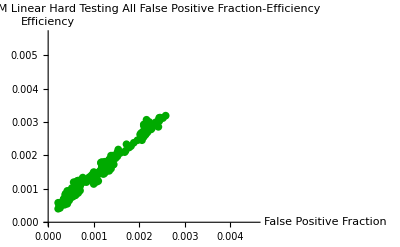

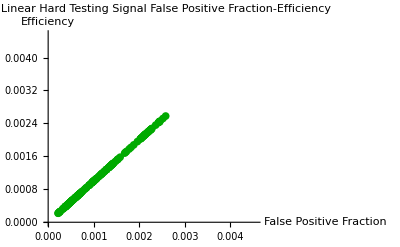

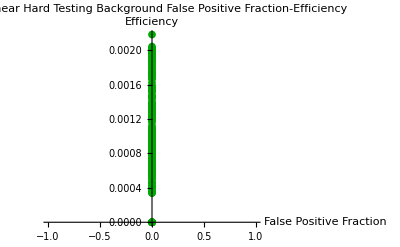

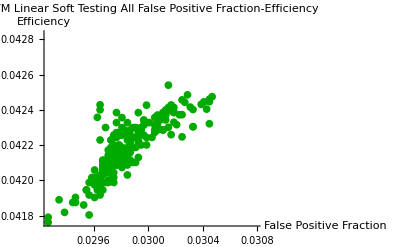

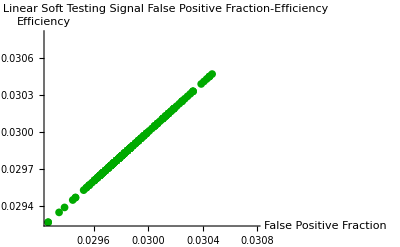

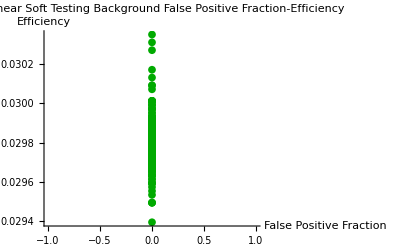

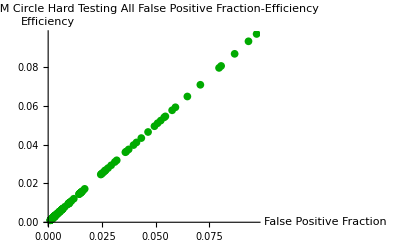

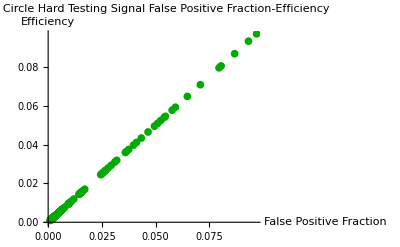

```mathematica
AllPlots[SVMFPEPlot,SVMAllRawData,SVMAllDataTypes]
```

### BDS

#### Number of Stumps-Efficiency

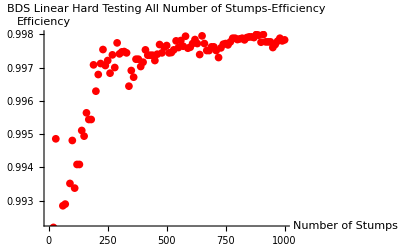

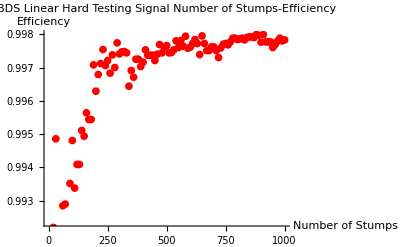

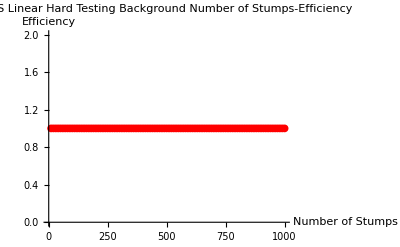

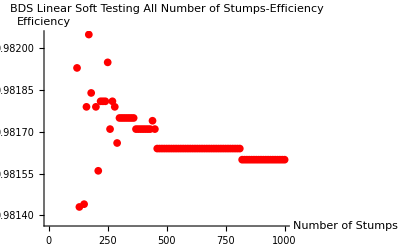

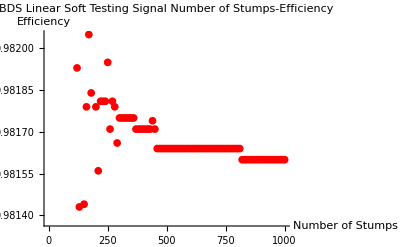

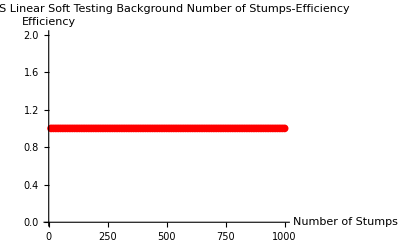

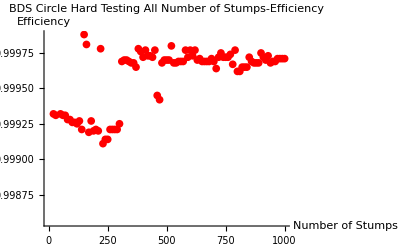

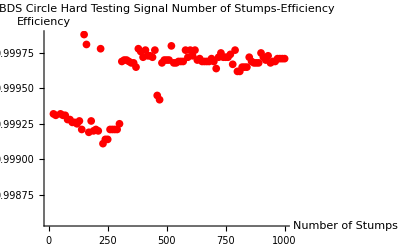

-Graphics-

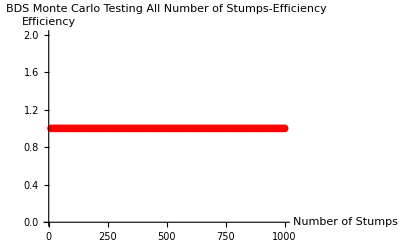

```mathematica
AllPlots[BDSSEPlot,BDSAllRawData,BDSAllDataTypes]
```

#### Number of Stumps-Distance

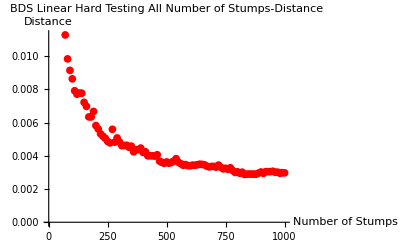

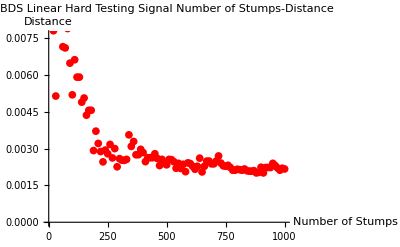

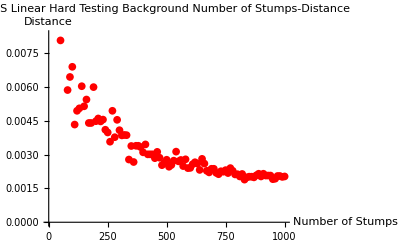

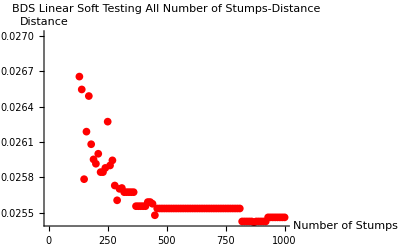

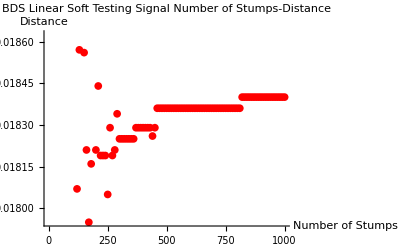

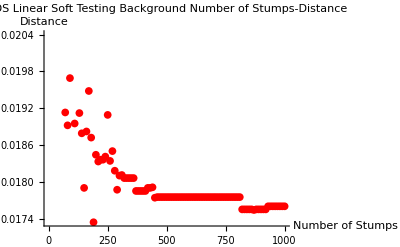

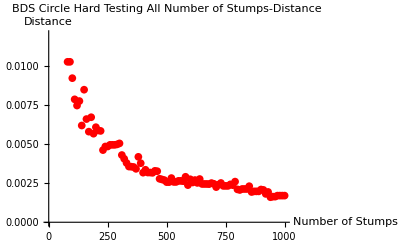

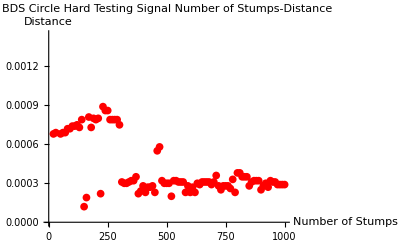

-Graphics-

-Graphics-

-Graphics-

«40 more identical outputs»

```mathematica
AllPlots[BDSSDPlot,BDSAllRawData,BDSAllDataTypes]
```

#### False Positive Fraction-Efficiency

```mathematica
AllPlots[BDSFPEPlot,BDSAllRawData,BDSAllDataTypes]
```

-Graphics-

-Graphics-

-Graphics-

«54 more identical outputs»

### BDT

#### Number of Trees-Efficiency

```mathematica
AllPlots[BDTTEPlot,BDTAllRawData,BDTAllDataTypes]
```

-Graphics-

-Graphics-

-Graphics-

«54 more identical outputs»

#### Number of Trees-Distance

```mathematica
AllPlots[BDTTDPlot,BDTAllRawData,BDTAllDataTypes]
```

-Graphics-

-Graphics-

-Graphics-

«54 more identical outputs»

#### False Positive Fraction-Efficiency

```mathematica
AllPlots[BDTFPEPlot,BDTAllRawData,BDTAllDataTypes]
```

-Graphics-

-Graphics-

-Graphics-

«54 more identical outputs»